```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/johann/Dropbox/projects/approximation

```mathematica
$MaxPrecision=Infinity
$MaxExtraPrecision=Infinity
```

∞

∞

```mathematica
N[Sin[10^22],24]
```

-0.852200849767188801772706

```mathematica
xPoints[b_,n_:10]:=Table[N[b+x,200],{x,-2π,+2π,1/n}]
plotAtXPoints[f_,b_,n_Integer, args___]:=ListPlot[f/@xPoints[b,n], args]
```

## Argument Reduction

### Exact Argument Reduction

```mathematica
argReduceExact[x_]:=Block[
{k=Abs[x]/π},
k-Round[k]]
Attributes[argReduceExact]={Listable,NumericFunction}
```

{Listable,NumericFunction}

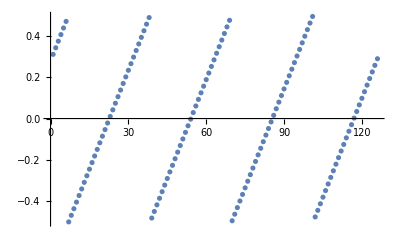

```mathematica
plotAtXPoints[argReduceExact,10^3]
```

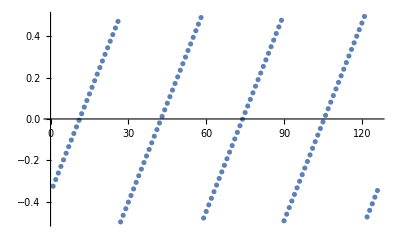

```mathematica
plotAtXPoints[argReduceExact,10^22]
```

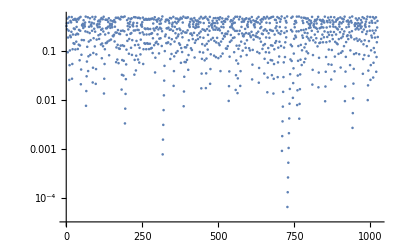

```mathematica
ListLogPlot[Table[Abs[argReduceExact[2^x]],{x,0,1023}]]
```

### Naive Method

The naive method used here is just the exact method from above, with an artificial limitation on the precision to $MachinePrecision.

```mathematica
$MachinePrecision
```

15.9546

```mathematica
argReduceNaive[x_]:=Block[
{k=N[SetPrecision[Abs[x],$MachinePrecision]/SetPrecision[π,$MachinePrecision],$MachinePrecision]},
k-Round[k]]
Attributes[argReduceNaive]={Listable,NumericFunction}
```

{Listable,NumericFunction}

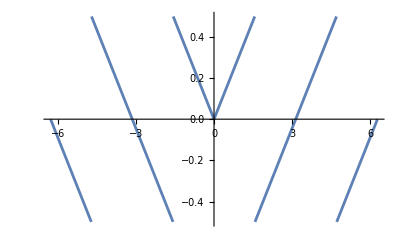

```mathematica
Plot[argReduceNaive[x],{x,-2π,2π}]
```

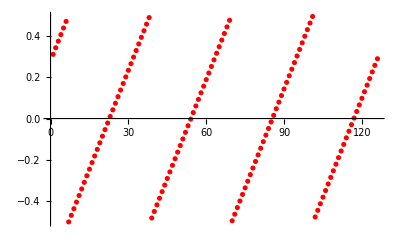

```mathematica
plotAtXPoints[argReduceNaive,10^3,10,PlotStyle->Red]
```

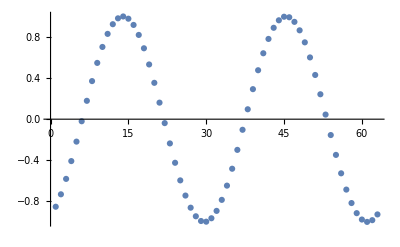

```mathematica
ListPlot[Sin[#]&/@xPoints[10^22,5]]
```

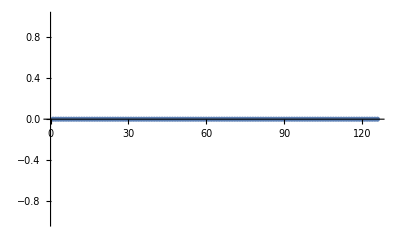

```mathematica
plotAtXPoints[argReduceNaive,10^22]
```

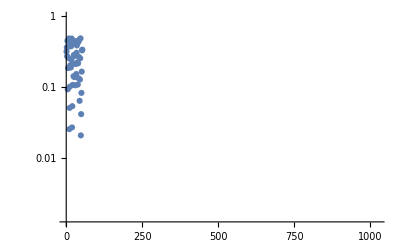

```mathematica
ListLogPlot[Table[Abs[argReduceNaive[2^x]],{x,0,1023}],PlotRange->{{0,1024},{-1,1}}]
```

```mathematica
Partition[Table[{x,Abs[argReduceNaive[2^x]-argReduceExact[2^x]]},{x,0,1023}],10]//TableForm
```

0
0. | 1
0. | 2
0. | 3
0. | 4
0. | 5
0. | 6
0. | 7
0. | 8
0. | 9
0.
10
0. | 11
0. | 12
0. | 13
0. | 14
0. | 15
0. | 16
0. | 17
0. | 18
0. | 19
0.
20
0. | 21
0. | 22
0. | 23
0. | 24
0. | 25
0. | 26
0. | 27
0. | 28
0. | 29
0.
30
0. | 31
0. | 32
0. | 33
0. | 34
0. | 35
0. | 36
0. | 37
0. | 38
0. | 39
0.
40
0. | 41
0. | 42
0. | 43
0. | 44
0. | 45
0. | 46
0. | 47
0. | 48
0. | 49
0.
50
0. | 51
0. | 52
0. | 53
0. | 54
0``-0.1049101186338301 | 55
0``-0.4059401142978113 | 56
0``-0.7069701099617925 | 57
0``-1.0080001056257737 | 58
0``-1.309030101289755 | 59
0``-1.6100600969537362
60
0``-1.9110900926177175 | 61
0``-2.2121200882816985 | 62
0``-2.5131500839456797 | 63
0``-2.814180079609661 | 64
0``-3.1152100752736422 | 65
0``-3.4162400709376235 | 66
0``-3.7172700666016025 | 67
0``-4.018300062265584 | 68
0``-4.319330057929565 | 69
0``-4.620360053593546
70
0``-4.9213900492575275 | 71
0``-5.222420044921509 | 72
0``-5.52345004058549 | 73
0``-5.824480036249471 | 74
0``-6.125510031913453 | 75
0``-6.426540027577434 | 76
0``-6.727570023241414 | 77
0``-7.028600018905395 | 78
0``-7.329630014569377 | 79
0``-7.630660010233358
80
0``-7.931690005897339 | 81
0``-8.23272000156132 | 82
0``-8.533749997225302 | 83
0``-8.834779992889283 | 84
0``-9.135809988553264 | 85
0``-9.436839984217245 | 86
0``-9.737869979881227 | 87
0``-10.038899975545208 | 88
0``-10.33992997120919 | 89
0``-10.64095996687317
90
0``-10.941989962537152 | 91
0``-11.243019958201133 | 92
0``-11.544049953865114 | 93
0``-11.845079949529095 | 94
0``-12.146109945193077 | 95
0``-12.447139940857058 | 96
0``-12.74816993652104 | 97
0``-13.04919993218502 | 98
0``-13.350229927849005 | 99
0``-13.651259923512987
100
0``-13.952289919176968 | 101
0``-14.253319914840949 | 102
0``-14.55434991050493 | 103
0``-14.855379906168912 | 104
0``-15.156409901832893 | 105
0``-15.457439897496874 | 106
0``-15.758469893160855 | 107
0``-16.059499888824835 | 108
0``-16.360529884488816 | 109
0``-16.661559880152797
110
0``-16.96258987581678 | 111
0``-17.26361987148076 | 112
0``-17.56464986714474 | 113
0``-17.865679862808722 | 114
0``-18.166709858472704 | 115
0``-18.467739854136685 | 116
0``-18.768769849800666 | 117
0``-19.069799845464647 | 118
0``-19.370829841128625 | 119
0``-19.671859836792606
120
0``-19.972889832456588 | 121
0``-20.27391982812057 | 122
0``-20.57494982378455 | 123
0``-20.87597981944853 | 124
0``-21.177009815112513 | 125
0``-21.478039810776494 | 126
0``-21.779069806440475 | 127
0``-22.080099802104456 | 128
0``-22.381129797768438 | 129
0``-22.68215979343242
130
0``-22.9831897890964 | 131
0``-23.28421978476038 | 132
0``-23.585249780424363 | 133
0``-23.886279776088344 | 134
0``-24.187309771752325 | 135
0``-24.488339767416306 | 136
0``-24.789369763080288 | 137
0``-25.09039975874427 | 138
0``-25.39142975440825 | 139
0``-25.69245975007223
140
0``-25.993489745736213 | 141
0``-26.294519741400194 | 142
0``-26.595549737064175 | 143
0``-26.896579732728156 | 144
0``-27.197609728392138 | 145
0``-27.49863972405612 | 146
0``-27.7996697197201 | 147
0``-28.10069971538408 | 148
0``-28.401729711048063 | 149
0``-28.702759706712044
150
0``-29.003789702376025 | 151
0``-29.304819698040006 | 152
0``-29.605849693703988 | 153
0``-29.90687968936797 | 154
0``-30.20790968503195 | 155
0``-30.50893968069593 | 156
0``-30.809969676359913 | 157
0``-31.110999672023894 | 158
0``-31.412029667687875 | 159
0``-31.713059663351856
160
0``-32.01408965901584 | 161
0``-32.31511965467982 | 162
0``-32.6161496503438 | 163
0``-32.91717964600778 | 164
0``-33.21820964167176 | 165
0``-33.519239637335744 | 166
0``-33.820269632999725 | 167
0``-34.12129962866371 | 168
0``-34.42232962432769 | 169
0``-34.72335961999167
170
0``-35.02438961565565 | 171
0``-35.32541961131963 | 172
0``-35.62644960698361 | 173
0``-35.927479602647594 | 174
0``-36.228509598311575 | 175
0``-36.52953959397556 | 176
0``-36.83056958963954 | 177
0``-37.13159958530352 | 178
0``-37.4326295809675 | 179
0``-37.73365957663148
180
0``-38.03468957229546 | 181
0``-38.335719567959444 | 182
0``-38.636749563623425 | 183
0``-38.93777955928741 | 184
0``-39.23880955495139 | 185
0``-39.53983955061537 | 186
0``-39.84086954627935 | 187
0``-40.14189954194333 | 188
0``-40.44292953760731 | 189
0``-40.743959533271294
190
0``-41.044989528935275 | 191
0``-41.34601952459926 | 192
0``-41.64704952026324 | 193
0``-41.94807951592722 | 194
0``-42.2491095115912 | 195
0``-42.55013950725518 | 196
0``-42.85116950291916 | 197
0``-43.152199498583144 | 198
0``-43.453229494247125 | 199
0``-43.75425948991111
200
0``-44.05528948557509 | 201
0``-44.35631948123907 | 202
0``-44.65734947690305 | 203
0``-44.95837947256703 | 204
0``-45.25940946823101 | 205
0``-45.560439463894994 | 206
0``-45.861469459558975 | 207
0``-46.16249945522296 | 208
0``-46.46352945088694 | 209
0``-46.76455944655091
210
0``-47.06558944221489 | 211
0``-47.366619437878875 | 212
0``-47.667649433542856 | 213
0``-47.96867942920684 | 214
0``-48.26970942487082 | 215
0``-48.5707394205348 | 216
0``-48.87176941619878 | 217
0``-49.17279941186276 | 218
0``-49.47382940752674 | 219
0``-49.774859403190725
220
0``-50.075889398854706 | 221
0``-50.37691939451869 | 222
0``-50.67794939018267 | 223
0``-50.97897938584665 | 224
0``-51.28000938151063 | 225
0``-51.58103937717461 | 226
0``-51.88206937283859 | 227
0``-52.183099368502575 | 228
0``-52.484129364166556 | 229
0``-52.78515935983054
230
0``-53.08618935549452 | 231
0``-53.3872193511585 | 232
0``-53.68824934682248 | 233
0``-53.98927934248646 | 234
0``-54.29030933815044 | 235
0``-54.591339333814425 | 236
0``-54.892369329478406 | 237
0``-55.19339932514239 | 238
0``-55.49442932080637 | 239
0``-55.79545931647035
240
0``-56.09648931213433 | 241
0``-56.39751930779831 | 242
0``-56.69854930346229 | 243
0``-56.999579299126275 | 244
0``-57.300609294790256 | 245
0``-57.60163929045424 | 246
0``-57.90266928611822 | 247
0``-58.2036992817822 | 248
0``-58.50472927744618 | 249
0``-58.80575927311016
250
0``-59.10678926877414 | 251
0``-59.407819264438125 | 252
0``-59.708849260102106 | 253
0``-60.00987925576609 | 254
0``-60.31090925143007 | 255
0``-60.61193924709405 | 256
0``-60.91296924275803 | 257
0``-61.21399923842201 | 258
0``-61.51502923408599 | 259
0``-61.816059229749975
260
0``-62.117089225413956 | 261
0``-62.41811922107794 | 262
0``-62.71914921674192 | 263
0``-63.0201792124059 | 264
0``-63.32120920806988 | 265
0``-63.62223920373386 | 266
0``-63.92326919939784 | 267
0``-64.22429919506183 | 268
0``-64.52532919072581 | 269
0``-64.8263591863898
270
0``-65.12738918205378 | 271
0``-65.42841917771776 | 272
0``-65.72944917338174 | 273
0``-66.03047916904572 | 274
0``-66.3315091647097 | 275
0``-66.63253916037368 | 276
0``-66.93356915603766 | 277
0``-67.23459915170164 | 278
0``-67.53562914736563 | 279
0``-67.8366591430296
280
0``-68.13768913869359 | 281
0``-68.43871913435757 | 282
0``-68.73974913002155 | 283
0``-69.04077912568553 | 284
0``-69.34180912134951 | 285
0``-69.6428391170135 | 286
0``-69.94386911267748 | 287
0``-70.24489910834146 | 288
0``-70.54592910400544 | 289
0``-70.84695909966942
290
0``-71.1479890953334 | 291
0``-71.44901909099737 | 292
0``-71.75004908666135 | 293
0``-72.05107908232533 | 294
0``-72.35210907798931 | 295
0``-72.65313907365329 | 296
0``-72.95416906931727 | 297
0``-73.25519906498126 | 298
0``-73.55622906064524 | 299
0``-73.85725905630922
300
0``-74.1582890519732 | 301
0``-74.45931904763718 | 302
0``-74.76034904330116 | 303
0``-75.06137903896514 | 304
0``-75.36240903462912 | 305
0``-75.6634390302931 | 306
0``-75.96446902595709 | 307
0``-76.26549902162107 | 308
0``-76.56652901728505 | 309
0``-76.86755901294903
310
0``-77.16858900861301 | 311
0``-77.46961900427699 | 312
0``-77.77064899994097 | 313
0``-78.07167899560496 | 314
0``-78.37270899126894 | 315
0``-78.67373898693292 | 316
0``-78.9747689825969 | 317
0``-79.27579897826088 | 318
0``-79.57682897392486 | 319
0``-79.87785896958884
320
0``-80.17888896525282 | 321
0``-80.4799189609168 | 322
0``-80.78094895658079 | 323
0``-81.08197895224477 | 324
0``-81.38300894790875 | 325
0``-81.68403894357273 | 326
0``-81.98506893923671 | 327
0``-82.28609893490069 | 328
0``-82.58712893056467 | 329
0``-82.88815892622866
330
0``-83.18918892189264 | 331
0``-83.49021891755662 | 332
0``-83.7912489132206 | 333
0``-84.09227890888458 | 334
0``-84.39330890454856 | 335
0``-84.69433890021254 | 336
0``-84.99536889587652 | 337
0``-85.2963988915405 | 338
0``-85.59742888720449 | 339
0``-85.89845888286847
340
0``-86.19948887853245 | 341
0``-86.50051887419643 | 342
0``-86.80154886986041 | 343
0``-87.10257886552439 | 344
0``-87.40360886118837 | 345
0``-87.70463885685236 | 346
0``-88.00566885251634 | 347
0``-88.30669884818032 | 348
0``-88.6077288438443 | 349
0``-88.90875883950828
350
0``-89.20978883517226 | 351
0``-89.51081883083624 | 352
0``-89.81184882650022 | 353
0``-90.1128788221642 | 354
0``-90.41390881782819 | 355
0``-90.71493881349217 | 356
0``-91.01596880915615 | 357
0``-91.31699880482013 | 358
0``-91.61802880048411 | 359
0``-91.9190587961481
360
0``-92.22008879181207 | 361
0``-92.52111878747606 | 362
0``-92.82214878314004 | 363
0``-93.12317877880402 | 364
0``-93.424208774468 | 365
0``-93.72523877013198 | 366
0``-94.02626876579596 | 367
0``-94.32729876145994 | 368
0``-94.62832875712392 | 369
0``-94.9293587527879
370
0``-95.23038874845189 | 371
0``-95.53141874411587 | 372
0``-95.83244873977985 | 373
0``-96.13347873544383 | 374
0``-96.43450873110781 | 375
0``-96.7355387267718 | 376
0``-97.03656872243577 | 377
0``-97.33759871809976 | 378
0``-97.63862871376374 | 379
0``-97.93965870942772
380
0``-98.2406887050917 | 381
0``-98.54171870075568 | 382
0``-98.84274869641966 | 383
0``-99.14377869208364 | 384
0``-99.44480868774762 | 385
0``-99.7458386834116 | 386
0``-100.04686867907559 | 387
0``-100.34789867473957 | 388
0``-100.64892867040355 | 389
0``-100.94995866606753
390
0``-101.25098866173151 | 391
0``-101.5520186573955 | 392
0``-101.85304865305947 | 393
0``-102.15407864872346 | 394
0``-102.45510864438744 | 395
0``-102.75613864005142 | 396
0``-103.0571686357154 | 397
0``-103.35819863137938 | 398
0``-103.65922862704336 | 399
0``-103.96025862270734
400
0``-104.26128861837132 | 401
0``-104.5623186140353 | 402
0``-104.86334860969929 | 403
0``-105.16437860536327 | 404
0``-105.46540860102725 | 405
0``-105.76643859669123 | 406
0``-106.06746859235521 | 407
0``-106.3684985880192 | 408
0``-106.66952858368317 | 409
0``-106.97055857934716
410
0``-107.27158857501114 | 411
0``-107.57261857067512 | 412
0``-107.8736485663391 | 413
0``-108.17467856200308 | 414
0``-108.47570855766706 | 415
0``-108.77673855333104 | 416
0``-109.07776854899502 | 417
0``-109.378798544659 | 418
0``-109.67982854032299 | 419
0``-109.98085853598697
420
0``-110.28188853165095 | 421
0``-110.58291852731493 | 422
0``-110.88394852297891 | 423
0``-111.1849785186429 | 424
0``-111.48600851430687 | 425
0``-111.78703850997086 | 426
0``-112.08806850563484 | 427
0``-112.38909850129882 | 428
0``-112.6901284969628 | 429
0``-112.99115849262678
430
0``-113.29218848829076 | 431
0``-113.59321848395474 | 432
0``-113.89424847961872 | 433
0``-114.1952784752827 | 434
0``-114.49630847094669 | 435
0``-114.79733846661067 | 436
0``-115.09836846227465 | 437
0``-115.39939845793863 | 438
0``-115.70042845360261 | 439
0``-116.0014584492666
440
0``-116.30248844493057 | 441
0``-116.60351844059456 | 442
0``-116.90454843625854 | 443
0``-117.20557843192252 | 444
0``-117.5066084275865 | 445
0``-117.80763842325048 | 446
0``-118.10866841891446 | 447
0``-118.40969841457844 | 448
0``-118.71072841024242 | 449
0``-119.0117584059064
450
0``-119.31278840157039 | 451
0``-119.61381839723437 | 452
0``-119.91484839289835 | 453
0``-120.21587838856233 | 454
0``-120.51690838422631 | 455
0``-120.8179383798903 | 456
0``-121.11896837555427 | 457
0``-121.41999837121826 | 458
0``-121.72102836688224 | 459
0``-122.02205836254622
460
0``-122.3230883582102 | 461
0``-122.62411835387418 | 462
0``-122.92514834953816 | 463
0``-123.22617834520214 | 464
0``-123.52720834086612 | 465
0``-123.8282383365301 | 466
0``-124.12926833219409 | 467
0``-124.43029832785807 | 468
0``-124.73132832352205 | 469
0``-125.03235831918603
470
0``-125.33338831485001 | 471
0``-125.634418310514 | 472
0``-125.93544830617797 | 473
0``-126.23647830184196 | 474
0``-126.53750829750594 | 475
0``-126.83853829316992 | 476
0``-127.1395682888339 | 477
0``-127.44059828449788 | 478
0``-127.74162828016186 | 479
0``-128.04265827582583
480
0``-128.3436882714898 | 481
0``-128.6447182671538 | 482
0``-128.94574826281777 | 483
0``-129.24677825848175 | 484
0``-129.54780825414574 | 485
0``-129.84883824980972 | 486
0``-130.1498682454737 | 487
0``-130.45089824113768 | 488
0``-130.75192823680166 | 489
0``-131.05295823246564
490
0``-131.35398822812962 | 491
0``-131.6550182237936 | 492
0``-131.95604821945759 | 493
0``-132.25707821512157 | 494
0``-132.55810821078555 | 495
0``-132.85913820644953 | 496
0``-133.1601682021135 | 497
0``-133.4611981977775 | 498
0``-133.76222819344147 | 499
0``-134.06325818910545
500
0``-134.36428818476944 | 501
0``-134.66531818043342 | 502
0``-134.9663481760974 | 503
0``-135.26737817176138 | 504
0``-135.56840816742536 | 505
0``-135.86943816308934 | 506
0``-136.17046815875332 | 507
0``-136.4714981544173 | 508
0``-136.77252815008129 | 509
0``-137.07355814574527
510
0``-137.37458814140925 | 511
0``-137.67561813707323 | 512
0``-137.9766481327372 | 513
0``-138.2776781284012 | 514
0``-138.57870812406517 | 515
0``-138.87973811972915 | 516
0``-139.18076811539314 | 517
0``-139.48179811105712 | 518
0``-139.7828281067211 | 519
0``-140.08385810238508
520
0``-140.38488809804906 | 521
0``-140.68591809371304 | 522
0``-140.98694808937702 | 523
0``-141.287978085041 | 524
0``-141.58900808070499 | 525
0``-141.89003807636897 | 526
0``-142.19106807203295 | 527
0``-142.49209806769693 | 528
0``-142.7931280633609 | 529
0``-143.0941580590249
530
0``-143.39518805468887 | 531
0``-143.69621805035285 | 532
0``-143.99724804601684 | 533
0``-144.29827804168082 | 534
0``-144.5993080373448 | 535
0``-144.90033803300878 | 536
0``-145.20136802867276 | 537
0``-145.50239802433674 | 538
0``-145.80342802000072 | 539
0``-146.1044580156647
540
0``-146.40548801132869 | 541
0``-146.70651800699267 | 542
0``-147.00754800265665 | 543
0``-147.30857799832063 | 544
0``-147.6096079939846 | 545
0``-147.9106379896486 | 546
0``-148.21166798531257 | 547
0``-148.51269798097655 | 548
0``-148.81372797664054 | 549
0``-149.11475797230452
550
0``-149.4157879679685 | 551
0``-149.71681796363248 | 552
0``-150.01784795929646 | 553
0``-150.31887795496044 | 554
0``-150.61990795062442 | 555
0``-150.9209379462884 | 556
0``-151.22196794195239 | 557
0``-151.52299793761637 | 558
0``-151.82402793328035 | 559
0``-152.12505792894433
560
0``-152.4260879246083 | 561
0``-152.7271179202723 | 562
0``-153.02814791593627 | 563
0``-153.32917791160025 | 564
0``-153.63020790726424 | 565
0``-153.93123790292822 | 566
0``-154.2322678985922 | 567
0``-154.53329789425618 | 568
0``-154.83432788992016 | 569
0``-155.13535788558414
570
0``-155.43638788124812 | 571
0``-155.7374178769121 | 572
0``-156.03844787257609 | 573
0``-156.33947786824007 | 574
0``-156.64050786390405 | 575
0``-156.94153785956803 | 576
0``-157.242567855232 | 577
0``-157.543597850896 | 578
0``-157.84462784655997 | 579
0``-158.14565784222395
580
0``-158.44668783788794 | 581
0``-158.74771783355192 | 582
0``-159.0487478292159 | 583
0``-159.34977782487988 | 584
0``-159.65080782054386 | 585
0``-159.95183781620784 | 586
0``-160.25286781187182 | 587
0``-160.5538978075358 | 588
0``-160.85492780319979 | 589
0``-161.15595779886377
590
0``-161.45698779452775 | 591
0``-161.75801779019173 | 592
0``-162.0590477858557 | 593
0``-162.3600777815197 | 594
0``-162.66110777718367 | 595
0``-162.96213777284765 | 596
0``-163.26316776851164 | 597
0``-163.56419776417562 | 598
0``-163.8652277598396 | 599
0``-164.16625775550358
600
0``-164.46728775116756 | 601
0``-164.76831774683154 | 602
0``-165.06934774249552 | 603
0``-165.3703777381595 | 604
0``-165.6714077338235 | 605
0``-165.97243772948747 | 606
0``-166.27346772515145 | 607
0``-166.57449772081543 | 608
0``-166.8755277164794 | 609
0``-167.1765577121434
610
0``-167.47758770780737 | 611
0``-167.77861770347135 | 612
0``-168.07964769913534 | 613
0``-168.38067769479932 | 614
0``-168.6817076904633 | 615
0``-168.98273768612728 | 616
0``-169.28376768179126 | 617
0``-169.58479767745524 | 618
0``-169.88582767311922 | 619
0``-170.1868576687832
620
0``-170.4878876644472 | 621
0``-170.78891766011117 | 622
0``-171.08994765577515 | 623
0``-171.39097765143913 | 624
0``-171.6920076471031 | 625
0``-171.9930376427671 | 626
0``-172.29406763843107 | 627
0``-172.59509763409505 | 628
0``-172.89612762975904 | 629
0``-173.19715762542302
630
0``-173.498187621087 | 631
0``-173.79921761675098 | 632
0``-174.10024761241496 | 633
0``-174.40127760807894 | 634
0``-174.70230760374292 | 635
0``-175.0033375994069 | 636
0``-175.3043675950709 | 637
0``-175.60539759073487 | 638
0``-175.90642758639885 | 639
0``-176.20745758206283
640
0``-176.5084875777268 | 641
0``-176.8095175733908 | 642
0``-177.11054756905477 | 643
0``-177.41157756471875 | 644
0``-177.71260756038274 | 645
0``-178.01363755604672 | 646
0``-178.3146675517107 | 647
0``-178.61569754737468 | 648
0``-178.91672754303866 | 649
0``-179.21775753870264
650
0``-179.51878753436662 | 651
0``-179.8198175300306 | 652
0``-180.1208475256946 | 653
0``-180.42187752135857 | 654
0``-180.72290751702255 | 655
0``-181.02393751268653 | 656
0``-181.3249675083505 | 657
0``-181.6259975040145 | 658
0``-181.92702749967847 | 659
0``-182.22805749534245
660
0``-182.52908749100644 | 661
0``-182.83011748667042 | 662
0``-183.1311474823344 | 663
0``-183.43217747799838 | 664
0``-183.73320747366236 | 665
0``-184.03423746932634 | 666
0``-184.33526746499032 | 667
0``-184.6362974606543 | 668
0``-184.9373274563183 | 669
0``-185.23835745198227
670
0``-185.53938744764625 | 671
0``-185.84041744331023 | 672
0``-186.1414474389742 | 673
0``-186.4424774346382 | 674
0``-186.74350743030217 | 675
0``-187.04453742596615 | 676
0``-187.34556742163014 | 677
0``-187.64659741729412 | 678
0``-187.9476274129581 | 679
0``-188.24865740862208
680
0``-188.54968740428606 | 681
0``-188.85071739995004 | 682
0``-189.15174739561402 | 683
0``-189.452777391278 | 684
0``-189.753807386942 | 685
0``-190.05483738260597 | 686
0``-190.35586737826995 | 687
0``-190.65689737393393 | 688
0``-190.9579273695979 | 689
0``-191.2589573652619
690
0``-191.55998736092587 | 691
0``-191.86101735658985 | 692
0``-192.16204735225384 | 693
0``-192.46307734791782 | 694
0``-192.7641073435818 | 695
0``-193.06513733924578 | 696
0``-193.36616733490976 | 697
0``-193.66719733057374 | 698
0``-193.96822732623772 | 699
0``-194.2692573219017
700
0``-194.5702873175657 | 701
0``-194.87131731322967 | 702
0``-195.17234730889365 | 703
0``-195.47337730455763 | 704
0``-195.7744073002216 | 705
0``-196.0754372958856 | 706
0``-196.37646729154957 | 707
0``-196.67749728721355 | 708
0``-196.97852728287754 | 709
0``-197.27955727854152
710
0``-197.5805872742055 | 711
0``-197.88161726986948 | 712
0``-198.18264726553346 | 713
0``-198.48367726119744 | 714
0``-198.78470725686142 | 715
0``-199.0857372525254 | 716
0``-199.3867672481894 | 717
0``-199.68779724385337 | 718
0``-199.98882723951735 | 719
0``-200.28985723518133
720
0``-200.5908872308453 | 721
0``-200.8919172265093 | 722
0``-201.19294722217327 | 723
0``-201.49397721783726 | 724
0``-201.79500721350124 | 725
0``-202.09603720916522 | 726
0``-202.3970672048292 | 727
0``-202.69809720049318 | 728
0``-202.99912719615716 | 729
0``-203.30015719182114
730
0``-203.60118718748512 | 731
0``-203.9022171831491 | 732
0``-204.2032471788131 | 733
0``-204.50427717447707 | 734
0``-204.80530717014105 | 735
0``-205.10633716580503 | 736
0``-205.407367161469 | 737
0``-205.708397157133 | 738
0``-206.00942715279697 | 739
0``-206.31045714846096
740
0``-206.61148714412494 | 741
0``-206.91251713978892 | 742
0``-207.2135471354529 | 743
0``-207.51457713111688 | 744
0``-207.81560712678086 | 745
0``-208.11663712244484 | 746
0``-208.41766711810882 | 747
0``-208.7186971137728 | 748
0``-209.0197271094368 | 749
0``-209.32075710510077
750
0``-209.62178710076475 | 751
0``-209.92281709642873 | 752
0``-210.2238470920927 | 753
0``-210.5248770877567 | 754
0``-210.82590708342067 | 755
0``-211.12693707908466 | 756
0``-211.42796707474864 | 757
0``-211.72899707041262 | 758
0``-212.0300270660766 | 759
0``-212.33105706174058
760
0``-212.63208705740456 | 761
0``-212.93311705306854 | 762
0``-213.23414704873252 | 763
0``-213.5351770443965 | 764
0``-213.8362070400605 | 765
0``-214.13723703572447 | 766
0``-214.43826703138845 | 767
0``-214.73929702705243 | 768
0``-215.0403270227164 | 769
0``-215.3413570183804
770
0``-215.64238701404437 | 771
0``-215.94341700970836 | 772
0``-216.24444700537234 | 773
0``-216.54547700103632 | 774
0``-216.8465069967003 | 775
0``-217.14753699236428 | 776
0``-217.44856698802826 | 777
0``-217.74959698369224 | 778
0``-218.05062697935622 | 779
0``-218.3516569750202
780
0``-218.6526869706842 | 781
0``-218.95371696634817 | 782
0``-219.25474696201215 | 783
0``-219.55577695767613 | 784
0``-219.8568069533401 | 785
0``-220.1578369490041 | 786
0``-220.45886694466807 | 787
0``-220.75989694033206 | 788
0``-221.06092693599604 | 789
0``-221.36195693166002
790
0``-221.662986927324 | 791
0``-221.96401692298798 | 792
0``-222.26504691865196 | 793
0``-222.56607691431594 | 794
0``-222.86710690997992 | 795
0``-223.1681369056439 | 796
0``-223.4691669013079 | 797
0``-223.77019689697187 | 798
0``-224.07122689263585 | 799
0``-224.37225688829983
800
0``-224.6732868839638 | 801
0``-224.9743168796278 | 802
0``-225.27534687529177 | 803
0``-225.57637687095576 | 804
0``-225.87740686661974 | 805
0``-226.17843686228372 | 806
0``-226.4794668579477 | 807
0``-226.78049685361168 | 808
0``-227.08152684927566 | 809
0``-227.38255684493964
810
0``-227.68358684060362 | 811
0``-227.9846168362676 | 812
0``-228.2856468319316 | 813
0``-228.58667682759557 | 814
0``-228.88770682325955 | 815
0``-229.18873681892353 | 816
0``-229.4897668145875 | 817
0``-229.7907968102515 | 818
0``-230.09182680591547 | 819
0``-230.39285680157946
820
0``-230.69388679724344 | 821
0``-230.99491679290742 | 822
0``-231.2959467885714 | 823
0``-231.59697678423538 | 824
0``-231.89800677989936 | 825
0``-232.19903677556334 | 826
0``-232.50006677122732 | 827
0``-232.8010967668913 | 828
0``-233.1021267625553 | 829
0``-233.40315675821927
830
0``-233.70418675388325 | 831
0``-234.00521674954723 | 832
0``-234.3062467452112 | 833
0``-234.6072767408752 | 834
0``-234.90830673653917 | 835
0``-235.20933673220316 | 836
0``-235.51036672786714 | 837
0``-235.81139672353112 | 838
0``-236.1124267191951 | 839
0``-236.41345671485908
840
0``-236.71448671052306 | 841
0``-237.01551670618704 | 842
0``-237.31654670185102 | 843
0``-237.617576697515 | 844
0``-237.918606693179 | 845
0``-238.21963668884297 | 846
0``-238.52066668450695 | 847
0``-238.82169668017093 | 848
0``-239.1227266758349 | 849
0``-239.4237566714989
850
0``-239.72478666716287 | 851
0``-240.02581666282686 | 852
0``-240.32684665849084 | 853
0``-240.62787665415482 | 854
0``-240.9289066498188 | 855
0``-241.22993664548278 | 856
0``-241.53096664114676 | 857
0``-241.83199663681074 | 858
0``-242.13302663247472 | 859
0``-242.4340566281387
860
0``-242.7350866238027 | 861
0``-243.03611661946667 | 862
0``-243.33714661513065 | 863
0``-243.63817661079463 | 864
0``-243.9392066064586 | 865
0``-244.2402366021226 | 866
0``-244.54126659778657 | 867
0``-244.84229659345056 | 868
0``-245.14332658911454 | 869
0``-245.44435658477852
870
0``-245.7453865804425 | 871
0``-246.04641657610648 | 872
0``-246.34744657177046 | 873
0``-246.64847656743444 | 874
0``-246.94950656309842 | 875
0``-247.2505365587624 | 876
0``-247.5515665544264 | 877
0``-247.85259655009037 | 878
0``-248.15362654575435 | 879
0``-248.45465654141833
880
0``-248.7556865370823 | 881
0``-249.0567165327463 | 882
0``-249.35774652841027 | 883
0``-249.65877652407426 | 884
0``-249.95980651973824 | 885
0``-250.26083651540222 | 886
0``-250.5618665110662 | 887
0``-250.86289650673018 | 888
0``-251.16392650239416 | 889
0``-251.46495649805814
890
0``-251.76598649372212 | 891
0``-252.0670164893861 | 892
0``-252.3680464850501 | 893
0``-252.66907648071407 | 894
0``-252.97010647637805 | 895
0``-253.27113647204203 | 896
0``-253.572166467706 | 897
0``-253.87319646337 | 898
0``-254.17422645903397 | 899
0``-254.47525645469796
900
0``-254.77628645036194 | 901
0``-255.07731644602592 | 902
0``-255.3783464416899 | 903
0``-255.67937643735388 | 904
0``-255.98040643301786 | 905
0``-256.28143642868184 | 906
0``-256.5824664243458 | 907
0``-256.8834964200098 | 908
0``-257.18452641567376 | 909
0``-257.48555641133777
910
0``-257.7865864070017 | 911
0``-258.08761640266573 | 912
0``-258.3886463983297 | 913
0``-258.6896763939937 | 914
0``-258.99070638965765 | 915
0``-259.29173638532166 | 916
0``-259.5927663809856 | 917
0``-259.8937963766496 | 918
0``-260.19482637231357 | 919
0``-260.4958563679776
920
0``-260.79688636364153 | 921
0``-261.09791635930554 | 922
0``-261.3989463549695 | 923
0``-261.6999763506335 | 924
0``-262.00100634629746 | 925
0``-262.30203634196147 | 926
0``-262.6030663376254 | 927
0``-262.90409633328943 | 928
0``-263.2051263289534 | 929
0``-263.5061563246174
930
0``-263.80718632028135 | 931
0``-264.10821631594536 | 932
0``-264.4092463116093 | 933
0``-264.7102763072733 | 934
0``-265.01130630293727 | 935
0``-265.3123362986013 | 936
0``-265.61336629426523 | 937
0``-265.91439628992924 | 938
0``-266.2154262855932 | 939
0``-266.5164562812572
940
0``-266.81748627692116 | 941
0``-267.11851627258517 | 942
0``-267.4195462682491 | 943
0``-267.72057626391313 | 944
0``-268.0216062595771 | 945
0``-268.3226362552411 | 946
0``-268.62366625090505 | 947
0``-268.92469624656906 | 948
0``-269.225726242233 | 949
0``-269.526756237897
950
0``-269.82778623356097 | 951
0``-270.128816229225 | 952
0``-270.42984622488893 | 953
0``-270.73087622055294 | 954
0``-271.0319062162169 | 955
0``-271.3329362118809 | 956
0``-271.63396620754486 | 957
0``-271.93499620320887 | 958
0``-272.2360261988728 | 959
0``-272.53705619453683
960
0``-272.8380861902008 | 961
0``-273.1391161858648 | 962
0``-273.44014618152875 | 963
0``-273.74117617719276 | 964
0``-274.0422061728567 | 965
0``-274.3432361685207 | 966
0``-274.64426616418467 | 967
0``-274.9452961598487 | 968
0``-275.24632615551263 | 969
0``-275.54735615117664
970
0``-275.8483861468406 | 971
0``-276.1494161425046 | 972
0``-276.45044613816856 | 973
0``-276.75147613383257 | 974
0``-277.0525061294965 | 975
0``-277.35353612516053 | 976
0``-277.6545661208245 | 977
0``-277.9555961164885 | 978
0``-278.25662611215245 | 979
0``-278.55765610781646
980
0``-278.8586861034804 | 981
0``-279.1597160991444 | 982
0``-279.46074609480837 | 983
0``-279.7617760904724 | 984
0``-280.06280608613633 | 985
0``-280.36383608180034 | 986
0``-280.6648660774643 | 987
0``-280.9658960731283 | 988
0``-281.26692606879226 | 989
0``-281.56795606445627
990
0``-281.8689860601202 | 991
0``-282.17001605578423 | 992
0``-282.4710460514482 | 993
0``-282.7720760471122 | 994
0``-283.07310604277615 | 995
0``-283.37413603844016 | 996
0``-283.6751660341041 | 997
0``-283.9761960297681 | 998
0``-284.27722602543207 | 999
0``-284.5782560210961
1000
0``-284.87928601676003 | 1001
0``-285.18031601242404 | 1002
0``-285.481346008088 | 1003
0``-285.782376003752 | 1004
0``-286.08340599941596 | 1005
0``-286.38443599507997 | 1006
0``-286.6854659907439 | 1007
0``-286.98649598640793 | 1008
0``-287.2875259820719 | 1009
0``-287.5885559777359
1010
0``-287.88958597339985 | 1011
0``-288.19061596906386 | 1012
0``-288.4916459647278 | 1013
0``-288.7926759603918 | 1014
0``-289.09370595605577 | 1015
0``-289.3947359517198 | 1016
0``-289.69576594738373 | 1017
0``-289.99679594304774 | 1018
0``-290.2978259387117 | 1019
0``-290.5988559343757

### Cody & Waite Method

For argument X, let  and , then

Cody & Waite suggest for & :

```mathematica
Subscript[C, 1]=N[3217/1024,$MachinePrecision]
Subscript[C, 2]=-8.908910206761537356617*10^-6
Subscript[C, 1]+Subscript[C, 2]
N[π,$MachinePrecision]
```

3.1416015625

-8.90891020676153735662×10^-6

3.14159265358979

3.14159265358979

```mathematica
argReduceCW[x_]:=Module[
{Y,XN,
C1=N[3217/1024,$MachinePrecision],
C2=-8.908910206761537356617*10^-6},
Y=Abs[x];
XN=Round[Y/N[π,$MachinePrecision]];
(Y-XN*C1)+XN*C2]
```

```mathematica
argReduceCW[1]
```

1

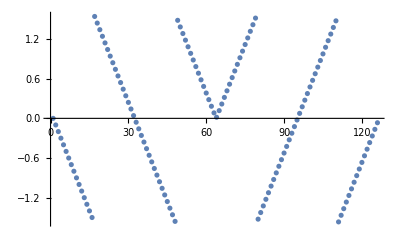

```mathematica
plotAtXPoints[argReduceCW,0]
```

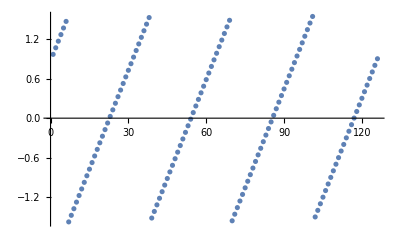

```mathematica
plotAtXPoints[argReduceCW,10^3]
```

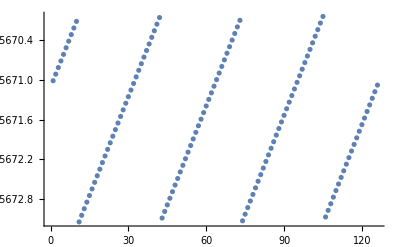

```mathematica
plotAtXPoints[argReduceCW,10^9]
```

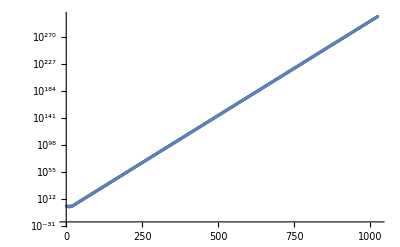

```mathematica
ListLogPlot[Table[Abs[argReduceCW[2^x]],{x,0,1023}]]
```

### Worst Cases

Muller (2016) describes the method for finding worst-cases arguments using continued fractions.

Start by reverse engineering the method for some of the cases calculated by Muller.  Table 11.2 gives the following value of x for

```mathematica
β=2;ex=849;p=53;K=Pi/2;
```

```mathematica
MantissaExponent[6381956970095103*2^797,2]
```

{6381956970095103/9007199254740992,850}

Since the mantissa above is < 1, the exponent in a normalized binary floating point representation will by 849, not 850.  Calculate successive convergents to , where  is the argument reduction constant.  (I use K here because C is reserved in Mathematica.)  The convergent  with the largest denominator Q< is the one corresponding to the floating point number with the smallest reduced argument.  In that case, the actual argument  and the reduced value  are given by:

#### Case 1

```mathematica
L=β^p;
conv=TakeWhile[Convergents[β^(ex-p+1)/K,200],Denominator[#]<=L&];
```

```mathematica
P=Numerator[Last[conv]]
Q=Denominator[Last[conv]]
```

3386417804515981120643892082331156599120239393299838035242121518428537554064774221620930267583474709602068045686026362989271814411863708499869721322715946622634302011697632972907922558892710830616034038541342154669787134871905353772776431251615694251273653

6381956970095103

```mathematica
Q*β^(ex-p+1)
```

5319372648326541416707296656673541083813475031793921822105998164685326343987747477646239125204069843392466931105720371047561653378447496736288905533500277726150903890962697774418679535123008556835980236851047840822029788166318932319835828816270258618761216

```mathematica
factorBy[2,Q*β^(ex-p+1)]
```

{2,6381956970095103,797}

#### Case 2

```mathematica
β=2;ex=848;p=53;K=Pi/4;
```

```mathematica
MantissaExponent[6381956970095103*2^796,2]
```

{6381956970095103/9007199254740992,849}

```mathematica
L=β^p;
conv=TakeWhile[Convergents[β^(ex-p+1)/K,200],Denominator[#]<=L&];
```

```mathematica
P=Numerator[Last[conv]]
Q=Denominator[Last[conv]]
```

3386417804515981120643892082331156599120239393299838035242121518428537554064774221620930267583474709602068045686026362989271814411863708499869721322715946622634302011697632972907922558892710830616034038541342154669787134871905353772776431251615694251273653

6381956970095103

```mathematica
Q*β^(ex-p+1)
```

2659686324163270708353648328336770541906737515896960911052999082342663171993873738823119562602034921696233465552860185523780826689223748368144452766750138863075451945481348887209339767561504278417990118425523920411014894083159466159917914408135129309380608

```mathematica
factorBy[2,Q*β^(ex-p+1)]
```

{2,6381956970095103,796}

#### General Algorithm

First, we’ll need a function to represent a number as an integer multiplied by a power of 2 or 10.

```mathematica
Clear[factorBy];
factorBy[b_Integer,n_]:=factorBy[b,n,0];
factorBy[b_Integer,n_,i_Integer]:=
If[FractionalPart[n]==0,
If[Divisible[Round[n],b],factorBy[b,Round[n]/b,i+1],{b,Floor[n],i}],
factorBy[b,n*b,i-1]
]
formatByFactor[b_,n_,i_]:=StringTemplate["`2` x (`1`)^(`3`)"][b,n,i]
```

This is the function that calculates the worst-case argument for a given number system (base, precision & range of exponents).

```mathematica
Clear[worstCase];
worstCase[K_,β_,p_,eMin_,eMax_]:=Module[
{L=β^p,wc,epsilon,wcEps,lowExp},
$MaxExtraPrecision=350;
wc[ex_]:=Last[TakeWhile[Convergents[β^(ex-p+1)/K,200],Denominator[#]<L&]];
wcEps[ex_]:=Module[{w,P,Q,x,ϵ},
w=wc[ex];
P=Numerator[w];
Q=Denominator[w];
x=Q*β^(ex-p+1);
ϵ=N[Q*K*Abs[P/Q-β^(ex-p+1)/K],$MachinePrecision];
{ex,x,ϵ,N[-Log[β,ϵ]]}
];
lowExp=N[Log[β,K]];
First[Sort[
Cases[
Table[wcEps[ex],{ex,eMin,eMax}],
{n_/;n>=lowExp,_,_,_}],
#1[[3]]<#2[[3]]&]]
]
```

```mathematica
cases={
{2,24,Pi/2,127},{2,24,Pi/4,127},{2,24,Log[2],127},{2,24,Log[10],127},
{10,10,Pi/2,99},{10,10,Pi/4,99},{10,10,Log[10],99},
{2,53,Pi/2,1023},{2,53,Pi/4,1023},{2,53,Log[2],1023},
{2,113,Pi/2,1024}
};
TableForm[cases]
```

2 | 24 | π/2 | 127
2 | 24 | π/4 | 127
2 | 24 | Log[2] | 127
2 | 24 | Log[10] | 127
10 | 10 | π/2 | 99
10 | 10 | π/4 | 99
10 | 10 | Log[10] | 99
2 | 53 | π/2 | 1023
2 | 53 | π/4 | 1023
2 | 53 | Log[2] | 1023
2 | 113 | π/2 | 1024

```mathematica
worstCaseColumns[{beta_,p_,k_,emax_}]:=Module[{wc},
wc=worstCase[k,beta,p,-emax+1,emax];
{beta,p,k,emax,Short[wc[[2]],0.3],formatByFactor@@factorBy[beta,N[wc[[2]],42]],NumberForm[wc[[4]],4]}
]
```

```mathematica
TableForm[worstCaseColumns/@cases,TableHeadings->{None,{"β","p","C","e_max","x","x (factored)","-ln(ϵ)"}}]
```

β | p | C | e_max | x | x (factored) | -ln(ϵ)
2 | 24 | π/2 | 127 | 7729178919«9»1184401408 | 16367173 x 2^72 | 29.21
2 | 24 | π/4 | 127 | 3864589459«9»0592200704 | 16367173 x 2^71 | 30.21
2 | 24 | Log[2] | 127 | 2221265/512 | 2221265 x 2^-9 | 31.62
2 | 24 | Log[10] | 127 | 9054133/262144 | 9054133 x 2^-18 | 28.41
10 | 10 | π/2 | 99 | 1031031439/125000 | 8248251512 x 10^-6 | 11.67
10 | 10 | π/4 | 99 | 1031031439/250000 | 4124125756 x 10^-6 | 11.97
10 | 10 | Log[10] | 99 | 7908257897«20»0000000000 | 7908257897 x 10^30 | 11.66
2 | 53 | π/2 | 1023 | 531937264«237»8618761216 | 6381956970095103 x 2^797 | 60.89
2 | 53 | π/4 | 1023 | 265968632«237»9309380608 | 6381956970095103 x 2^796 | 61.89
2 | 53 | Log[2] | 1023 | 861178801«147»1372789760 | 2630846436817885 x 2^500 | 66.78
2 | 113 | π/2 | 1024 | 512436415«255»7530165248 | 3073997040896496544881086095976867 x 2^798 | 122.8

This is a reproduction of Table 11.2 from Muller using the function worstCase above.  The factored values of x in lines 3, 10 & 11 are different, but represent the same numbers:

```mathematica
factorBy[2,8885060*2^-11]
```

{2,2221265,-9}

```mathematica
factorBy[2,5261692873635770*2^499]
```

{2,2630846436817885,500}

```mathematica
3073997040896496544881086095976867*2
```

6147994081792993089762172191953734

#### Lefevre & Muller

Lefevre & Muller (2001) give some worst-case arguments for Sin in the ranges [1/32,1] & [1,2].

```mathematica
x1=2^^0.01111111100110110011101110011100111010000111101101101
x2=2^^1.1001001000011111101101010100010001000010110100011000
```

0.498462

1.5708

```mathematica
BaseForm[Sin[x1],2]
```

0.011110100110001100101_2

```mathematica
BaseForm[Sin[x2],2]
```

1._2

```mathematica
N[Sin[x2],100]
```

1.

### Ng

For an argument x, let

where  and the fractional part of y is .  Then , the reduced argument, is

#### This doesn’t work in floating-point, because of limited precision, but let’s try it in Mathematica.

```mathematica
argReduceNg[x_]:=With[
{y=2*Abs[x]/Pi},
(y-Round[N[y,200]])*π/2
]
```

```mathematica
argReduceNg[2π]
```

0

```mathematica
Precision[argReduceNg[2π]]
```

∞

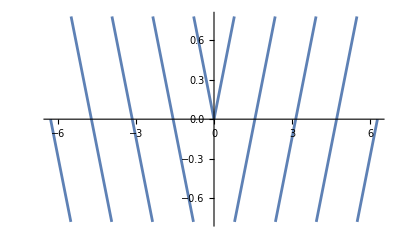

```mathematica
Plot[argReduceNg[x],{x,-2Pi,2Pi}]
```

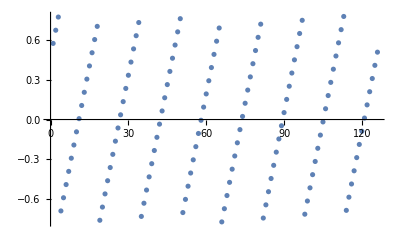

```mathematica
plotAtXPoints[argReduceNg,10^9]
```

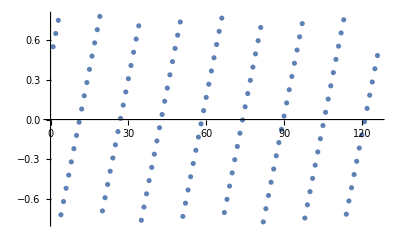

```mathematica
plotAtXPoints[argReduceNg,10^22]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3721683358689787356392605288764896593293752292965+11692013098647223345629478661730264157247460343808/π.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -7443366717379574712785210577529793186587504585930+23384026197294446691258957323460528314494920687616/π.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -14886733434759149425570421155059586373175009171860+46768052394588893382517914646921056628989841375232/π.

General::stop: Further output of N::meprec will be suppressed during this calculation.

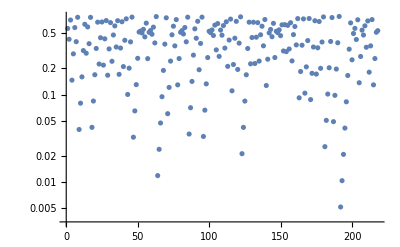

```mathematica
ListLogPlot[Table[Abs[argReduceNg[2^x]],{x,0,1023}]]
```

Plot::precw: The precision of the argument function ({Sin[π (1/2+0.63661977236758134307553505349005744813783858296182579499066937623558719053690614036045521106501234382429137090703183214757164738445831461151186964292679935691695986774963631029231098558770123075486957 Abs[x])]-0}) is less than WorkingPrecision (250.).

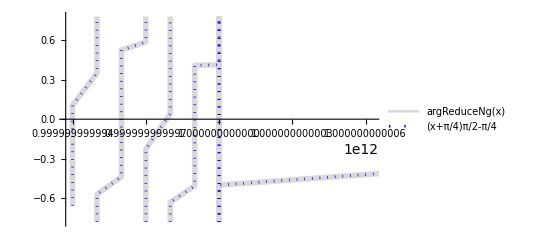

```mathematica
Plot[{argReduceNg[x],Mod[x+Pi/4,Pi/2]-Pi/4},{x,10^12-2Pi,10^12+2Pi},
PlotStyle->{{LightGray,Thickness[0.01]},{Dotted,Blue}},
PlotLegends->"Expressions",
WorkingPrecision->250]
```

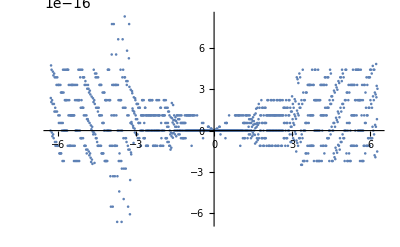

```mathematica
ListPlot[
Table[{x,argReduceNg[x]-(Mod[Abs[x]+Pi/4,Pi/2]-Pi/4)},{x,-2Pi,2Pi,0.01}]
]
```

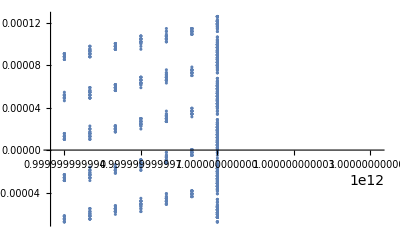

```mathematica
ListPlot[
Table[{x,argReduceNg[x]-(Mod[Abs[x]+Pi/4,Pi/2]-Pi/4)},{x,10^12-2Pi,10^12+2Pi,0.01}]
]
```

```mathematica
mySin[x_]:=Block[{intPart,fracPart,quadrant},
fracPart=Mod[x,Pi/2];
intPart=Floor[x/(π/2)];
quadrant=intPart-4*Floor[intPart/4];
{fracPart,quadrant};
Switch[quadrant,
0,Sin[fracPart],
1,Sin[π/2-fracPart],
2,-Sin[π-fracPart],
3,-Sin[π/2-fracPart]
]
]
```

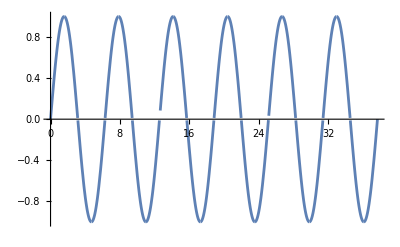

```mathematica
Plot[mySin[x],{x,0,12Pi}]
```

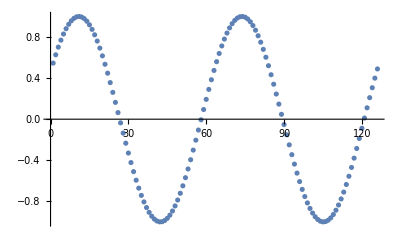

```mathematica
plotAtXPoints[mySin,10^9]
```

```mathematica
plotAtXPoints[(mySin[#]-Sin[#])&,10^9]
```

-Graphics-

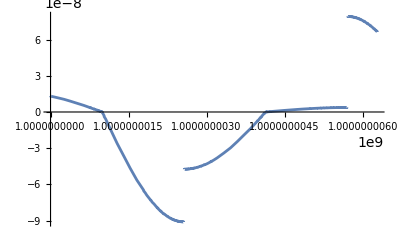

```mathematica
Plot[mySin[x]-Sin[x],{x,10^9,10^9+2Pi}]
```

```mathematica
Table[N[Mod[argReduce[x]+Pi/4,Pi/4]-Mod[x,Pi/4],250],{x,10^12,10^12+2Pi,0.1}]
```

{0.000088031,0.0000129439,-0.0000621433,-0.0000675531,0.0000491074,-0.0000259797,0.0000906807,0.0000178208,0.000012411,-0.0000626761,0.0000539843,-0.0000211028,0.0000955577,0.0000901478,0.0000150607,-0.0000577992,0.0000588613,-0.0000162258,-0.0000216357,0.0000950248,0.0000199377,-0.0000551495,0.000061511,0.0000583284,-0.0000167587,0.0000999017,0.0000248146,-0.0000502725,-0.0000556824,0.0000609781,-0.000014109,0.000104779,0.0000296916,0.0000242817,-0.0000508054,0.0000658551,-9.23205×10^-6,0.000107428,0.000104246,0.0000291587,-0.0000459284,0.000070732,-4.3551×10^-6,-9.76494×10^-6,0.000106896,0.0000318084,-0.0000410515,0.000075609,0.0000701991,-4.88799×10^-6,0.000111772,0.0000366854,-0.0000384018,-0.0000438116,0.0000750761,-1.10392×10^-8,0.000116649,0.0000415623,0.0000361525,-0.0000389347,0.0000777258,2.63869×10^-6,0.000121526}

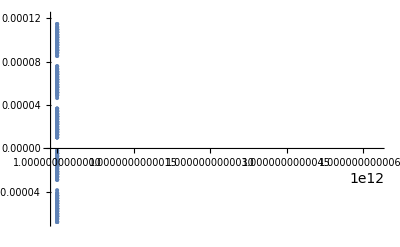

```mathematica
$MaxPrecision=250;
ListPlot[
Table[{x,N[Mod[argReduce[x]+Pi/4,Pi/4],250]-N[Mod[x,Pi/4],250]},{x,10^12,10^12+2Pi,0.01}]
]
```

```mathematica
X=6381956970095103*2^797
```

5319372648326541416707296656673541083813475031793921822105998164685326343987747477646239125204069843392466931105720371047561653378447496736288905533500277726150903890962697774418679535123008556835980236851047840822029788166318932319835828816270258618761216

```mathematica
N[X,24]
```

5.3193726483265414167073×10^255

```mathematica
$MaxPrecision=Infinity
y=N[X*2/π,1000]
k=Round[y]
f=N[y-k,24]
r=N[π*f/2,16]
```

∞

3.386417804515981120643892082331156599120239393299838035242121518428537554064774221620930267583474709602068045686026362989271814411863708499869721322715946622634302011697632972907922558892710830616034038541342154669787134871905353772776431251615694251273653000000000000000000298394250374806504539316094750403781620846457442077549608740784312381139422500142911419792677714492317546373552279294497247825693457617400032624054850329851938343514811343496751804865064350275232621118842261808203372436701277516029557109483118583713403237189990674993880235556967468842435045642784453060260612404578487199160161337079902953500423241482760840917394277894112592462654271975061434810817622999790623743301597977030163216011019299188350502621221818577017209358889485146481632281597768036710965044972291878117370610191781181317826788325576606016950412376610099641855205110008736512874215256613229130398536754177307661438609490378769970000394029790274641926626212755081848081750515071794933703277368977914198160421006×10^255

3386417804515981120643892082331156599120239393299838035242121518428537554064774221620930267583474709602068045686026362989271814411863708499869721322715946622634302011697632972907922558892710830616034038541342154669787134871905353772776431251615694251273653

2.98394250374806504539316×10^-19

4.687165924254628×10^-19

```mathematica
N[argReduce[N[X,1000]],16]
```

4.687165924254628×10^-19

```mathematica
Log[2,f]
```

-61.53941406564364073565491

```mathematica
Log[10,2^52]//N
```

15.6536

```mathematica
M=52;
x=10^Floor[M*Log[10,2]];
maxBits=M+174;
digits=RealDigits[2/Pi,2,maxBits][[1]];
dA=digits[[1;;(M-2)]];
dB=digits[[(M-1);;(M+173)]];
dC=digits[[(M+174);;]];
B=FromDigits[dB,2];
```

```mathematica
bParts=FromDigits[#,2]&/@Partition[dB,24]
xParts=FromDigits[#,2]&/@Partition[RealDigits[x,2][[1]],24]
```

{5548016,10313543,13947767,224650,5661937,934151,16336270}

{14901161,3252224}

```mathematica
FromDigits[xParts,2]
```

1000000000000000

```mathematica
factors={
PadLeft[bParts,Length[bParts]+Length[xParts]-1],
PadLeft[xParts,Length[bParts]+Length[xParts]-1]};
intermediateProducts={
Prepend[Table[bParts[[i]]*xParts[[2]],{i,1,Length[bParts]}],0],
Append[Table[bParts[[i]]*xParts[[1]],{i,1,Length[bParts]}],0]
};
sums={Table[intermediateProducts[[1]][[i]]+intermediateProducts[[2]][[i]],{i,1,Length[intermediateProducts[[1]]]}]};
```

```mathematica
Grid[
Join[factors,intermediateProducts,sums],
Alignment->".",
Dividers->{False,{False,False,True,False,True,False}}
]
```

0 | 5548016 | 10313543 | 13947767 | 224650 | 5661937 | 934151 | 16336270
0 | 0 | 0 | 0 | 0 | 0 | 14901161 | 3252224
0 | 18043390787584 | 33541952069632 | 45361262583808 | 730612121600 | 18413887397888 | 3038068301824 | 53129209364480
82671879646576 | 153683764723423 | 207837921657487 | 3347545818650 | 84369434808857 | 13919934449311 | 243429389409470 | 0
82671879646576 | 171727155511007 | 241379873727119 | 48708808402458 | 85100046930457 | 32333821847199 | 246467457711294 | 53129209364480

## GSL

If the GNU Scientific Library is compiled, we can call its  function from Mathematica:

```mathematica
gslSin=ForeignFunctionLoad["/usr/local/lib/libgsl","gsl_sf_sin",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

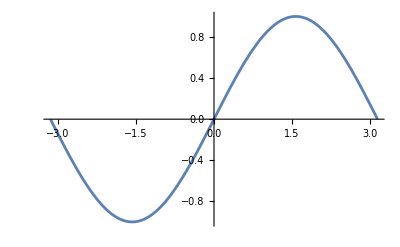

```mathematica
Plot[gslSin[x],{x,-3.14,3.14}]
```

It’s accurate to machine precision, or pretty close.

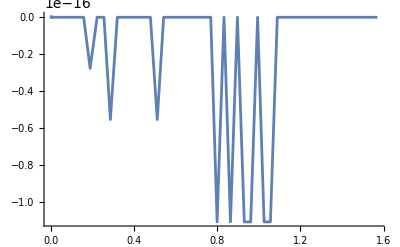

```mathematica
Plot[gslSin[x]-Sin[x],{x,0,Pi/2},WorkingPrecision->24,
MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}}]
```

Even at moderately large arguments:

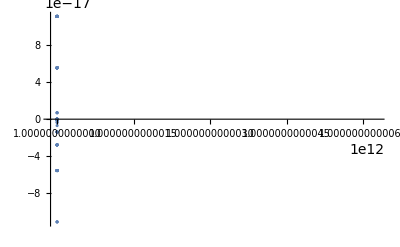

```mathematica
ListPlot[Table[{x,gslSin[x]-Sin[x]},{x,10^12,10^12+2π,0.01}]]
```

```mathematica
Max[Table[Abs[gslSin[x]-Sin[x]],{x,10^9,10^9+2π,0.01}]]
```

1.11022×10^-16

But not at really huge arguments:

```mathematica
gslSin[10^22]
```

-8.58809×10^65

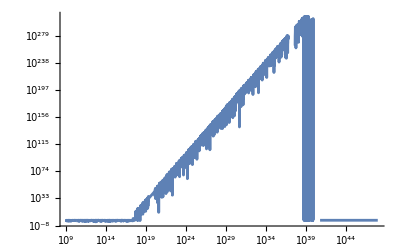

```mathematica
LogLogPlot[gslSin[x],{x,10^9,10^48}]
```

```mathematica
$MaxPrecision=200;
p=N[10^15,32];
Precision[p]
points=Table[{N[x,32],N[gslSin[x],32]},{x,p,p+2Pi,N[0.01,32]}]
ListPlot[points]
```

32.

{{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.787594},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.704625},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.610661},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.507167},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.395759},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.278176},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.156252},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,0.0318891},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.092971},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.21638},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.336413},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.451196},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.558939},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.657959},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.746712},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.823813},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.888059},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.938447},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.97419},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.994732},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.999751},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.98917},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.963152},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.922106},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.86667},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.797709},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.716301},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.623716},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.521397},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.410942},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.294075},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.172618},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,-0.0484682},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.0764382},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.200152},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.320742},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.436327},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.545104},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.645374},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.735573},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.814295},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.880309},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.932586},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.970311},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.992894},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.999984},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.991469},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.967482},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.928399},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.874828},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.807605},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.72778},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.636599},{1.×10^15,0.535483},{1.×10^15,0.535483},{1.×10^15,0.535483},{1.×10^15,0.535483}}

BinCounts::step: The bin step size -0.475048 is expected to be positive.

Mean::rectt: Rectangular array expected at position 1 in Mean[0.00148588].

Part::pkspec1: The expression Which[(0.00148588 BinCounts[{{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},{1.×10^15,0.858273},«4»,{1.×10^15,0.787594},{1.×10^15,0.787594},«663»},{«1»},{«1»}])/Mean[0.00148588]<2,1,Charting`CommonDump`density>10,2,True,3] cannot be used as a part specification.

-Graphics-

```mathematica
Precision[points[[1,1]]]
```

MachinePrecision

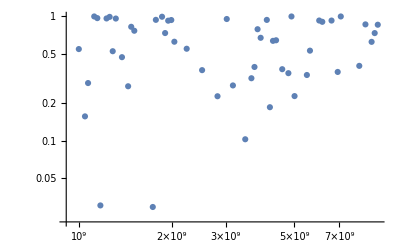

```mathematica
ListLogLogPlot[Table[{10^x,Sin[10^x]},{x,9,10,0.01}]]
```

```mathematica
ListLogLogPlot[Table[{10^x,gslSin[10^x]},{x,9,10,0.01}]]
```

-Graphics-

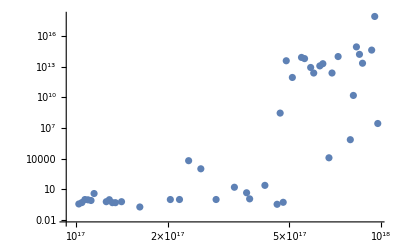

```mathematica
ListLogLogPlot[Table[{10^x,gslSin[10^x]},{x,17,18,0.01}]]
```

```mathematica
points=Table[{10^x,gslSin[10^x]},{x,Log[10,2.25*10^17],Log[10,2.3*10^17],0.00001}];
```

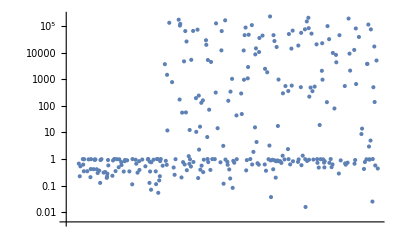

```mathematica
ListLogLogPlot[points]
```

This is the source for the GSL  function:

```mathematica
CellPrint[Cell[Import["/Users/johann/Dropbox/projects/approximation/refs/gsl_sin.c","Text"],"Program"]]
```

/*-*-*-*-*-*-*-*-*-*-*-* Functions with Error Codes *-*-*-*-*-*-*-*-*-*-*-*/

/* I would have prefered just using the library sin() function.
 * But after some experimentation I decided that there was
 * no good way to understand the error; library sin() is just a black box.
 * So we have to roll our own.
 */
int
gsl_sf_sin_e(double x, gsl_sf_result * result)
{
  /* CHECK_POINTER(result) */

  {
    const double P1 = 7.85398125648498535156e-1;
    const double P2 = 3.77489470793079817668e-8;
    const double P3 = 2.69515142907905952645e-15;

    const double sgn_x = GSL_SIGN(x);
    const double abs_x = fabs(x);

    if(abs_x < GSL_ROOT4_DBL_EPSILON) {
      const double x2 = x*x;
      result->val = x * (1.0 - x2/6.0);
      result->err = fabs(x*x2*x2 / 100.0);
      return GSL_SUCCESS;
    }
    else {
      double sgn_result = sgn_x;
      double y = floor(abs_x/(0.25*M_PI));
      int octant = y - ldexp(floor(ldexp(y,-3)),3);
      int stat_cs;
      double z;

      if(GSL_IS_ODD(octant)) {
        octant += 1;
        octant &= 07;
        y += 1.0;
      }

      if(octant > 3) {
        octant -= 4;
        sgn_result = -sgn_result;
      }

      z = ((abs_x - y * P1) - y * P2) - y * P3;

      if(octant == 0) {
        gsl_sf_result sin_cs_result;
        const double t = 8.0*fabs(z)/M_PI - 1.0;
        stat_cs = cheb_eval_e(&sin_cs, t, &sin_cs_result);
        result->val = z * (1.0 + z*z * sin_cs_result.val);
      }
      else { /* octant == 2 */
        gsl_sf_result cos_cs_result;
        const double t = 8.0*fabs(z)/M_PI - 1.0;
        stat_cs = cheb_eval_e(&cos_cs, t, &cos_cs_result);
        result->val = 1.0 - 0.5*z*z * (1.0 - z*z * cos_cs_result.val);
      }

      result->val *= sgn_result;

      if(abs_x > 1.0/GSL_DBL_EPSILON) {
        result->err = fabs(result->val);
      }
      else if(abs_x > 100.0/GSL_SQRT_DBL_EPSILON) {
        result->err = 2.0 * abs_x * GSL_DBL_EPSILON * fabs(result->val);
      }
      else if(abs_x > 0.1/GSL_SQRT_DBL_EPSILON) {
        result->err = 2.0 * GSL_SQRT_DBL_EPSILON * fabs(result->val);
      }
      else {
        result->err = 2.0 * GSL_DBL_EPSILON * fabs(result->val);
      }

      return stat_cs;
    }
  }
}

### GSL Angle Reduction

#### Mathematica Version

I’ll try to reproduce the angle-reduction algorithm from the GSL Sin function in Mathematica.

```mathematica
Clear[gslY,gslZ,gslT,ldexp,octant,processOctant]
```

```mathematica
ldexp[x_,c_]:=x*2^c;
```

```mathematica
octant[x_]:=With[{y=Floor[Abs[x]/(π/4)]},
y - ldexp[Floor[ldexp[y,-3]],3] 
]
```

```mathematica
Clear[processOctant]
processOctant[n_?OddQ]:=Mod[BitAnd[n+1,7]+1,4]
processOctant[n_?EvenQ]:=Mod[n,4]
```

```mathematica
gslY[x_]:=If[OddQ[octant[x]],Floor[Abs[x]/(π/4)]+1,Floor[Abs[x]/(π/4)]]
```

```mathematica
gslZ[x_]:=With[{
P1= 7.85398125648498535156*10^-1,
P2= 3.77489470793079817668*10^-8,
P3= 2.69515142907905952645*10^-15,
y = gslY[x]},
(*((Abs[x] - y * P1) - y * P2) - y * P3]*)
result=Abs[x];
result-=y*P1;
result-=y*P2;
result-=y*P3;
result]
```

```mathematica
gslT[x_]:=8/π*Abs[gslZ[x]] - 1
```

```mathematica
intToOct[n_Integer]:=n-8*Floor[n/8]
```

```mathematica
Table[intToOct[n],{n,0,20}]
```

{0,1,2,3,4,5,6,7,0,1,2,3,4,5,6,7,0,1,2,3,4}

Y gives the integer number of multiples of π/4 < x, and octant reduces that number mod 8:

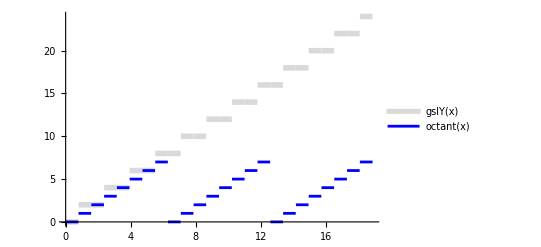

```mathematica
Plot[{gslY[x],octant[x]},{x,0,6Pi},PlotLegends->"Expressions",
PlotStyle->{{LightGray,Thickness[0.01]},{Medium,Blue}}]
```

```mathematica
Table[{n,processOctant[n]},{n,0,7}]//TableForm
```

0 | 0
1 | 3
2 | 2
3 | 1
4 | 0
5 | 3
6 | 2
7 | 1

P1, P2 & P3 add up to π/4:

```mathematica
P1= 7.85398125648498535156*10^-1;
P2= 3.77489470793079817668*10^-8;
P3= 2.69515142907905952645*10^-15;
TableForm[Transpose[{{"P1","P2","P3","P1+P2+P3","π/4"},{DecimalForm[P1,DigitBlock->5],DecimalForm[P2,DigitBlock->5],DecimalForm[P3,DigitBlock->5],DecimalForm[N[P1+P2+P3,34],DigitBlock->5],DecimalForm[N[Pi/4,34],DigitBlock->5]}}]]
```

P1 | 0.78539 81256 48498 53516
P2 | 0.00000 00377 48947 07930 79817 67
P3 | 0.00000 00000 00002 69515 14290 79059 5264
P1+P2+P3 | 0.78539 81633 97448 30962
π/4 | 0.78539 81633 97448 30961 56608 45819 8757

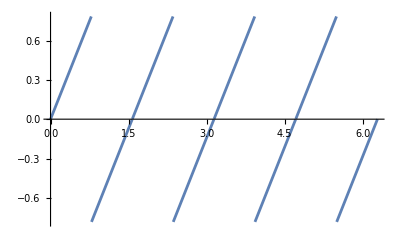

```mathematica
Plot[gslZ[x],{x,0,2Pi}]
```

```mathematica
argReduce2[x_]:=Mod[x+Pi/4,Pi/2]-Pi/4
```

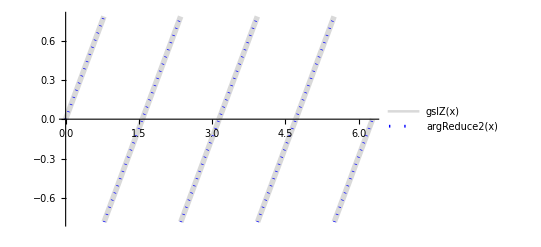

```mathematica
Plot[{gslZ[x],argReduce2[x]},{x,0,2Pi},PlotLegends->"Expressions",
PlotStyle->{{LightGray,Thickness[0.01]},{Dotted,Blue}}
]
```

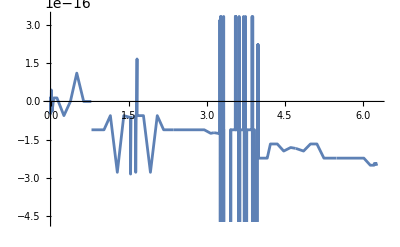

```mathematica
Plot[gslZ[x]-argReduce2[x],{x,0,2Pi}]
```

But at large arguments appears to be off quite a bit:

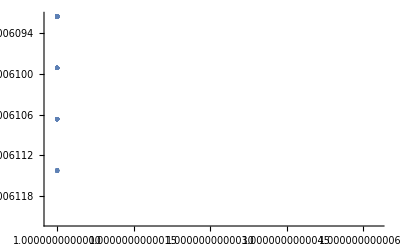

```mathematica
ListPlot[
Table[
{x,gslZ[x]-argReduce2[x]},{x,10^12,10^12+2Pi,0.01}]
]
```

```mathematica
gslReduce[x_]:=N[(gslT[x]+1)*π/8,50]
```

```mathematica
gslReduce2[x_]:=If[
OddQ[octant[x]],N[(-gslT2[x]+1)*π/8,50],N[(gslT2[x]+1)*π/8,50]]
```

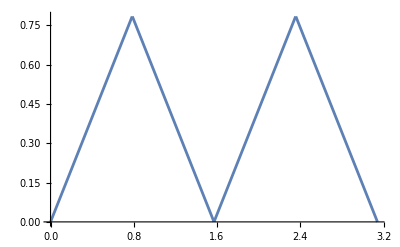

```mathematica
Plot[gslReduce[x],{x,0,π}]
```

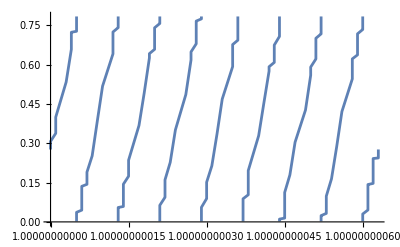

```mathematica
Plot[gslReduce[x],{x,10^10,2π+10^10}]
```

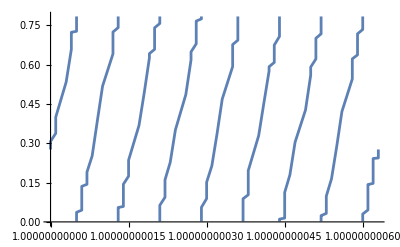

```mathematica
Plot[gslReduce2[x],{x,10^10,2π+10^10}]
```

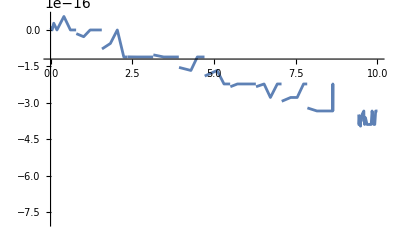

```mathematica
Plot[gslReduce[x]-Mod[x,π/4],{x,0,10}]
```

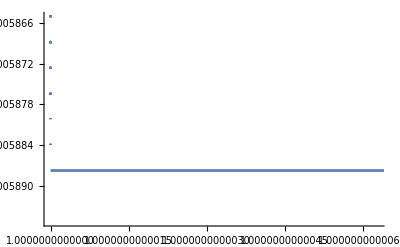

```mathematica
Plot[gslReduce[x]-N[Mod[x,π/4],24],{x,10^12,2π+10^12}]
```

Why is the error in this so large?

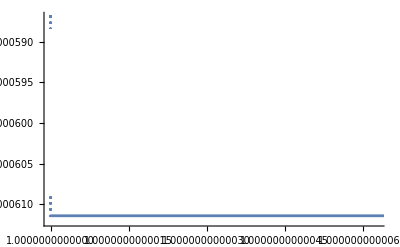

```mathematica
Plot[gslReduce2[x]-N[Mod[x,π/4],24],{x,10^12,2π+10^12}]
```

#### C Version

My version of the angle-reduction logic from GSL Sin, as a separate C function.

```mathematica
CellPrint[Cell[Import["/Users/johann/Dropbox/projects/approximation/sin/angle_reduction.c","Text"],"Program"]]
```

#include <gsl/gsl_math.h>

// This extracts the angle-reduction logic from
// gsl_sf_sin in the specfunc/trig.c file from GSL.

double gslReduceBase(double x) {
  const double P1 = 7.85398125648498535156e-1;
  const double P2 = 3.77489470793079817668e-8;
  const double P3 = 2.69515142907905952645e-15;

  const double abs_x = fabs(x);

  double y = floor(abs_x / (0.25 * M_PI));
  double z = ((abs_x - y * P1) - y * P2) - y * P3;
  double t = 8.0 * fabs(z) / M_PI - 1.0;

  return t;
}

// The function gslReducebase maps each octant
// onto [-1, +1].  So scale it to [0, Pi/4].

double gslReduce(double x) {
  double y = gslReduceBase(x);
  y = (y + 1)*M_PI_4/2;
  return y;
}

```mathematica
gslReduceExt=ForeignFunctionLoad["./sin/libmysin","gslReduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

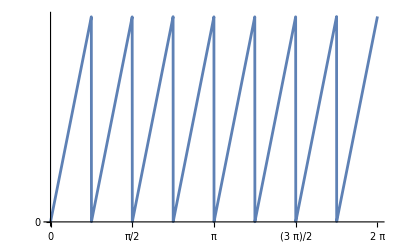

```mathematica
Plot[gslReduceExt[x],{x,0,2Pi},Ticks->{Table[n*Pi/4,{n,0,8}],{-1,0,1}}]
```

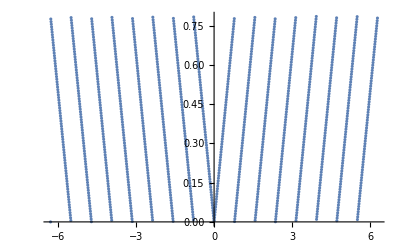

```mathematica
ListPlot[Table[{x,gslReduceExt[x]},{x,-2Pi,2Pi,0.01}]]
```

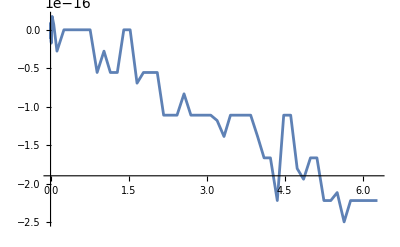

```mathematica
Plot[gslReduceExt[x]-N[Mod[x,π/4],24],{x,0,2π}]
```

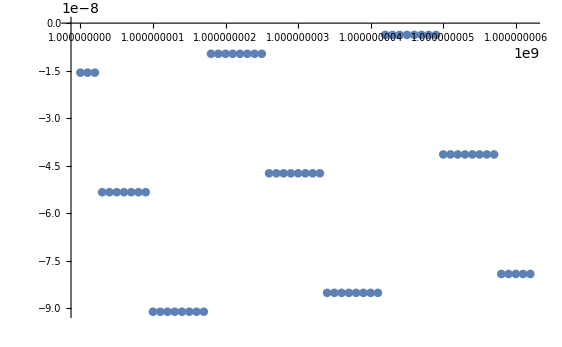

```mathematica
ListPlot[
Table[{x,gslReduceExt[x]-N[Mod[x,π/4]]},{x,10^9,2π+10^9,0.1}]
]
```

```mathematica
$MaxExtraPrecision=200;
disp[x_]:=DecimalForm[x,{18,17},DigitBlock->3,NumberSeparator->" "]
x=N[2π+10^12];
a=gslReduceExt[x];
b=Mod[x,π/4];
d=a-b;
{
disp[N[a,24]],
disp[N[b,24]]
}//TableForm
disp[N[d,24]]
```

0.127 791 222 081 075 40
0.127 807 617 187 500000

-0.000 016 395 106 424 62

```mathematica
{#,Precision[Symbol[#]],Accuracy[Symbol[#]]}&/@{"a","b","d"}//TableForm
```

a | MachinePrecision | 16.8481
b | MachinePrecision | 16.848
d | MachinePrecision | 20.7399

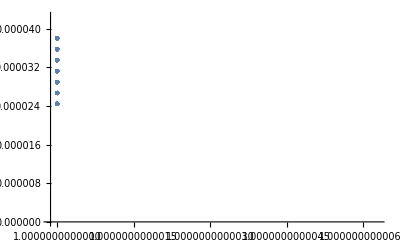

```mathematica
ListPlot[Table[
{x,gslReduceExt[x]-gslReduce[x]},{x,10^12,10^12+2Pi,0.01}
]]
```

### GSL Chebyshev Approximation

```mathematica
CellPrint[Cell[Import["/Users/johann/Dropbox/projects/approximation/refs/gsl_cheb.c","Text"],"Program"]]
```

/* data for a Chebyshev series over a given interval */

struct gsl_cheb_series_struct {

  double * c;   /* coefficients                */
  size_t order; /* order of expansion          */
  double a;     /* lower interval point        */
  double b;     /* upper interval point        */

  /* The following exists (mostly) for the benefit
   * of the implementation. It is an effective single
   * precision order, for use in single precision
   * evaluation. Users can use it if they like, but
   * only they know how to calculate it, since it is
   * specific to the approximated function. By default,
   * order_sp = order.
   * It is used explicitly only by the gsl_cheb_eval_mode
   * functions, which are not meant for casual use.
   */
  size_t order_sp;

  /* Additional elements not used by specfunc */

  double * f;   /* function evaluated at chebyschev points  */
};
typedef struct gsl_cheb_series_struct gsl_cheb_series;

/* Chebyshev expansion for f(t) = g((t+1)Pi/8), -1<t<1
 * g(x) = (sin(x)/x - 1)/(x*x)
 */
static double sin_data[12] = {
  -0.3295190160663511504173,
   0.0025374284671667991990,
   0.0006261928782647355874,
  -4.6495547521854042157541e-06,
  -5.6917531549379706526677e-07,
   3.7283335140973803627866e-09,
   3.0267376484747473727186e-10,
  -1.7400875016436622322022e-12,
  -1.0554678305790849834462e-13,
   5.3701981409132410797062e-16,
   2.5984137983099020336115e-17,
  -1.1821555255364833468288e-19
};
static cheb_series sin_cs = {
  sin_data,
  11,
  -1, 1,
  11
};

/* Chebyshev expansion for f(t) = g((t+1)Pi/8), -1<t<1
 * g(x) = (2(cos(x) - 1)/(x^2) + 1) / x^2
 */
static double cos_data[11] = {
  0.165391825637921473505668118136,
 -0.00084852883845000173671196530195,
 -0.000210086507222940730213625768083,
  1.16582269619760204299639757584e-6,
  1.43319375856259870334412701165e-7,
 -7.4770883429007141617951330184e-10,
 -6.0969994944584252706997438007e-11,
  2.90748249201909353949854872638e-13,
  1.77126739876261435667156490461e-14,
 -7.6896421502815579078577263149e-17,
 -3.7363121133079412079201377318e-18
};
static cheb_series cos_cs = {
  cos_data,
  10,
  -1, 1,
  10
};

double
gsl_cheb_eval (const gsl_cheb_series * cs, const double x)
{
  size_t i;
  double d1 = 0.0;
  double d2 = 0.0;

  double y = (2.0 * x - cs->a - cs->b) / (cs->b - cs->a);
  double y2 = 2.0 * y;

  for (i = cs->order; i >= 1; i--)
    {
      double temp = d1;
      d1 = y2 * d1 - d2 + cs->c[i];
      d2 = temp;
    }

  return y * d1 - d2 + 0.5 * cs->c[0];
}

These are the functions that are directly approximated by Chebyshev series in GSL:

```mathematica
t[x_]:=π/8(x+1)
```

```mathematica
f[t_]:=(Sin[t]/t-1)/t^2
```

```mathematica
g[t_]:=(2(Cos[t]-1)/t^2+1)/t^2
```

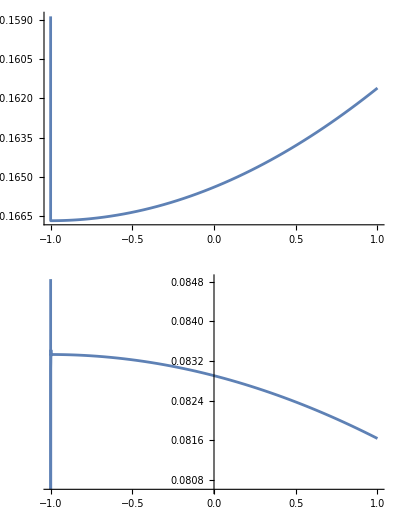

```mathematica
GraphicsColumn[{
Plot[f[t[x]],{x,-1,1},PlotLabel->""],
Plot[g[t[x]],{x,-1,1},PlotLabel->""]
}]
```

Which are then transformed to approximate Sin & Cos over the first octant:

```mathematica
(*
const double t = 8.0*fabs(z)/M_PI - 1.0;
stat_cs = cheb_eval_e(&sin_cs, t, &sin_cs_result);
result->val = z * (1.0 + z*z * sin_cs_result.val);
*)
gslResultSin[x_]:=With[
{z=gslZ[x]},
z*(1+z^2 f[t[x]])
]
```

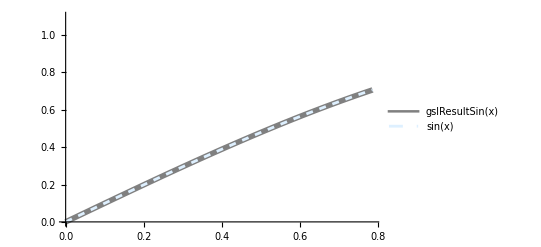

```mathematica
Plot[{gslResultSin[x],Sin[x]},{x,0,Pi/4},
PlotRange->{{0,Pi/4},{0,1.1}},
PlotStyle->{{Gray,Thickness[0.01]},{Dashed,LightBlue}},
PlotLegends->"Expressions"]
```

```mathematica
(*
const  double  t = 8.0*fabs (z)/M_PI - 1.0;
stat_cs = cheb_eval _e (& cos_cs, t, & cos_cs _result);
result -> val = 1.0 - 0.5*z*z * (1.0 - z*z * cos_cs _result . val);
*)
gslResultCos[x_]:=With[
{z=gslZ[x]},
1-z^2/2(1-z^2 g[t[x]])
]
```

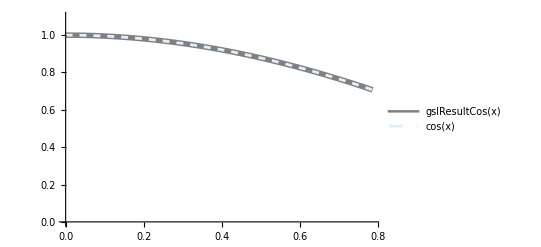

```mathematica
Plot[{gslResultCos[x],Cos[x]},{x,0,Pi/4},
PlotRange->{{0,Pi/4},{0,1.1}},
PlotStyle->{{Gray,Thickness[0.01]},{Dashed,LightBlue}},
PlotLegends->"Expressions"]
```

## Calling Assembly Language

### sin1.s

This is the most basic approximation, using just the first two terms of the Taylor series, as a proof that we can write a dynamic library in ARM assembly and call it from C and from Mathematica.

```mathematica
CellPrint[Cell[Import["sin/sin1.s","Text"],"Program"]]
```

// sin1.s
// Approximate Sin(x) by the Taylor series to degree 3.

.global _sin_1
.p2align 2			// Make sure everything is aligned properly

.text

_sin_1:
        fmul    d1, d0, d0              // d1 = d0^2
        fmul    d1, d1, d0              // d1 = d0^3
        fmov    d2, #6
        fdiv    d1, d1, d2              // d1 = d0^3/6
        fsub    d0, d0, d1              // d0 = d0 - d0^3/6
        ret

```mathematica
sin1=ForeignFunctionLoad["./sin/libmysin","sin_1",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
sin1[0]
```

0.

```mathematica
sin1[N[Pi/2]]
```

0.924832

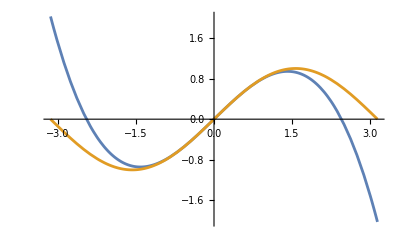

```mathematica
Plot[{sin1[x],Sin[x]},{x,-Pi,Pi}]
```

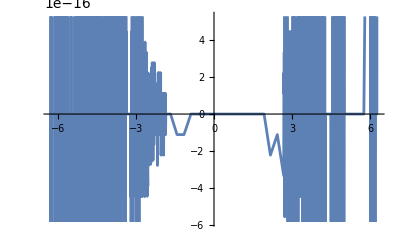

```mathematica
Plot[sin1[x]-(x-x^3/6),{x,-2π,2π},WorkingPrecision->24]
```

### sin2.s

```mathematica
This is a Chebyshev approximation to Sin, without any angle reduction.
```

```mathematica
CellPrint[Cell[Import["sin/sin2.s","Text"],"Program"]]
```

// sin2.s
// Approximate Sin(x) by Chebyshev approximation

.global         _sin_2
.p2align        2			// Make sure everything is aligned properly

        .macro  LOADVAL reg, name
        adrp    x0, \name@GOTPAGE
        ldr     x0, [x0, \name@GOTPAGEOFF]
        ldr     \reg, [x0]
        .endm

.text

_sin_2:
        LOADVAL d1, a0
        LOADVAL d2, a1
        LOADVAL d3, a2
        LOADVAL d4, a3
        LOADVAL d5, a4
        LOADVAL d6, a5
        LOADVAL d7, a6
        LOADVAL d8, a7
        LOADVAL d9, a8
        LOADVAL d10, a9
        LOADVAL d11, a10
        LOADVAL d12, a11
        LOADVAL d13, a12
        LOADVAL d14, a13

        fmadd   d13, d14, d0, d13
        fmadd   d12, d13, d0, d12
        fmadd   d11, d12, d0, d11
        fmadd   d10, d11, d0, d10
        fmadd   d9, d10, d0, d9
        fmadd   d8, d9, d0, d8
        fmadd   d7, d8, d0, d7
        fmadd   d6, d7, d0, d6
        fmadd   d5, d6, d0, d5
        fmadd   d4, d5, d0, d4
        fmadd   d3, d4, d0, d3
        fmadd   d2, d3, d0, d2
        fmadd   d1, d2, d0, d1

        fmov    d0, d1
        ret

.p2align        2
.data
a0:	.double	+3.15159609307366933583264e-17
a1:	.double	+9.99999999999992137463981e-1
a2:	.double	+3.24848403977218879514298e-13
a3:	.double	-1.66666666671945646405887e-1
a4:	.double	+4.46929940061919965152147e-11
a5:	.double	+8.33333310712103651500584e-3
a6:	.double	+7.39903364746182917886826e-10
a7:	.double	-1.98414335571346275936300e-4
a8:	.double	+2.51241790401253696723421e-9
a9:	.double	+2.75303544969185019022074e-6
a10:	.double	+2.00650971121911487700779e-9
a11:	.double	-2.60546344930653900663444e-8
a12:	.double	+3.11243537080303902068867e-10
a13:	.double	+1.12392760716968552199773e-10

```mathematica
$Failed
```

$Failed

```mathematica
$Failed
```

$Failed

```mathematica
Clear[sin2]
sin2=ForeignFunctionLoad["./sin/libmysin","sin_2",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

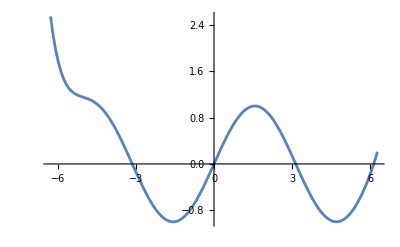

```mathematica
Plot[sin2[x],{x,-2Pi,2Pi}]
```

### sin3.s

```mathematica
CellPrint[Cell[Import["sin/sin3.s","Text"],"Program"]]
```

// sin3.s
// Approximate Sin(x) by Chebyshev approximation

.global         _sin_3
.p2align        2		// Make sure everything is aligned properly

        .macro  LOADVAL reg, name
        adrp    x0, \name@GOTPAGE
        ldr     x0, [x0, \name@GOTPAGEOFF]
        ldr     \reg, [x0]
        .endm

.text

_sin_3:
        mov     w1, wzr         // we're going to use w1 to keep some flags
        fmov    d4, #2          // we're going to mulitply & divide by 2 later

        fcmp    d0, #0.0
        bge     pos             // x < 0, return -Sin(-x)
        mov     w1, 0x0001      // 1 in w1 bit 1 will mean negate the result at the end
        fneg    d0, d0

pos:
        LOADVAL d1, c2Pi        // d1 = 2*Pi
        fcmp    d0, d1
        ble     inrange
        fdiv    d3, d0, d1      // d0 > 2*Pi
        frintz  d3, d3          // floor
        fmsub   d0, d3, d1, d0

inrange:                        // d0 < 2*Pi
        fdiv    d1, d1, d4      // d1 = Pi
        fcmp    d0, d1
        ble     first_half      // 0 <= x <= Pi
        fsub    d0, d0, d1      // d0 = d0 - Pi
        eor     w1, w1, 0x0001  // toggle 1st bit of w1, to negate the final answer

first_half:
        fdiv    d1, d1, d4      // d1 = Pi/2
        fcmp    d0, d1
        ble     approx          // 0 <= d0 <= Pi/2 - calculate the approximation
        // Pi/2 < d0 <= Pi - return Sin(Pi-x)
        fmul    d1, d1, d4      // d1 = Pi
        fsub    d0, d1, d0      // d0 = Pi - d0

approx:
        LOADVAL d1, a0
        LOADVAL d2, a1
        LOADVAL d3, a2
        LOADVAL d4, a3
        LOADVAL d5, a4
        LOADVAL d6, a5
        LOADVAL d7, a6
        LOADVAL d8, a7
        LOADVAL d9, a8
        LOADVAL d10, a9
        LOADVAL d11, a10
        LOADVAL d12, a11
        LOADVAL d13, a12
        LOADVAL d14, a13

        fmadd   d13, d14, d0, d13
        fmadd   d12, d13, d0, d12
        fmadd   d11, d12, d0, d11
        fmadd   d10, d11, d0, d10
        fmadd   d9, d10, d0, d9
        fmadd   d8, d9, d0, d8
        fmadd   d7, d8, d0, d7
        fmadd   d6, d7, d0, d6
        fmadd   d5, d6, d0, d5
        fmadd   d4, d5, d0, d4
        fmadd   d3, d4, d0, d3
        fmadd   d2, d3, d0, d2
        fmadd   d1, d2, d0, d1

        fmov    d0, d1
        and     w1, w1, 0x0001
        cmp     w1, #0
        beq     end
        fneg    d0, d0

end:
        ret

.p2align        2
.data
a0:	.double	+3.15159609307366933583264e-17
a1:	.double	+9.99999999999992137463981e-1
a2:	.double	+3.24848403977218879514298e-13
a3:	.double	-1.66666666671945646405887e-1
a4:	.double	+4.46929940061919965152147e-11
a5:	.double	+8.33333310712103651500584e-3
a6:	.double	+7.39903364746182917886826e-10
a7:	.double	-1.98414335571346275936300e-4
a8:	.double	+2.51241790401253696723421e-9
a9:	.double	+2.75303544969185019022074e-6
a10:	.double	+2.00650971121911487700779e-9
a11:	.double	-2.60546344930653900663444e-8
a12:	.double	+3.11243537080303902068867e-10
a13:	.double	+1.12392760716968552199773e-10

c2Pi:   .double +6.28318530717958647692529

        /*
Questions:
        Is there a simpler way to multiply & divide FP registers by 2?
        Simple way to keep a flag and negate a FP value conditional on the flag?
        */

```mathematica
Clear[sin3]
sin3=ForeignFunctionLoad["./sin/libmysin","sin_3",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

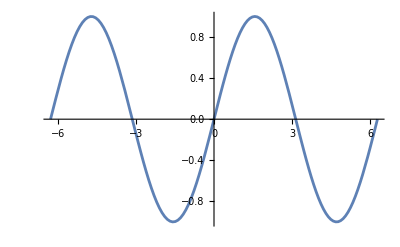

```mathematica
Plot[sin3[x],{x,-2Pi,2Pi}]
```

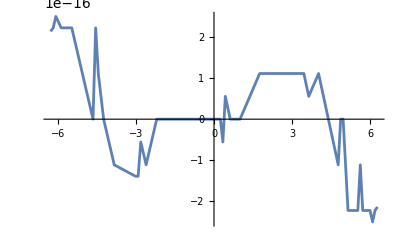

```mathematica
Plot[Sin[x]-sin3[x],{x,-2Pi,2Pi}]
```

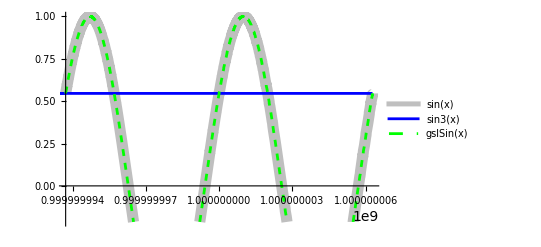

```mathematica
Plot[{Sin[x],sin3[x],gslSin[x]},{x,10^9-2Pi,10^9+2Pi},
PlotLegends->"Expressions",
MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}},
PlotStyle->{{Thickness[0.02],Opacity[0.5],Gray},{Blue},{Dashed,Green}}]
```

```mathematica
|
```

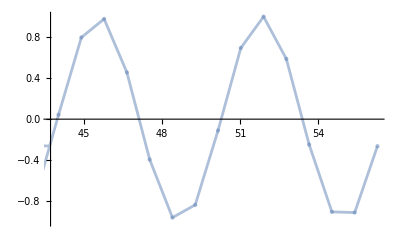

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

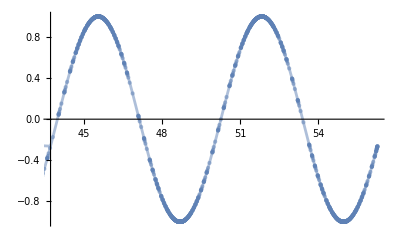

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]},MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}}]
```

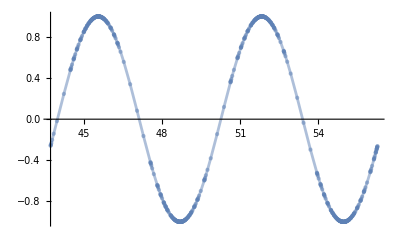

```mathematica
Plot[gslSin[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

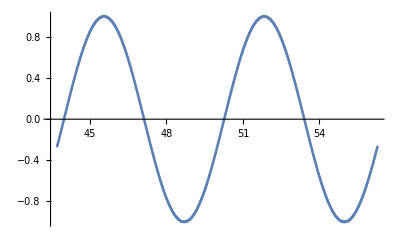

```mathematica
ListPlot[Table[{x,sin3[x]},{x,50-2Pi,50+2Pi,0.01}]]
```

```mathematica
reduce=ForeignFunctionLoad["./sin/libmysin","reduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

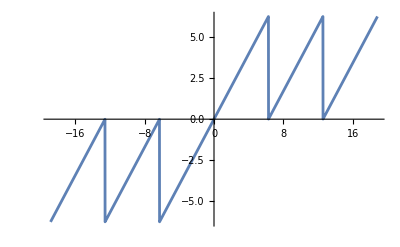

```mathematica
Plot[reduce[x],{x,-6Pi,6Pi}]
```

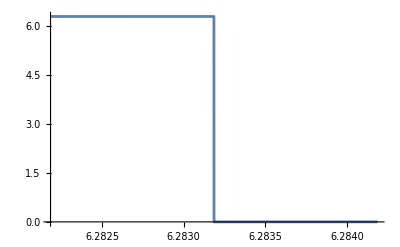

```mathematica
Plot[reduce[x],{x,2Pi-0.001,2Pi+0.001}]
```

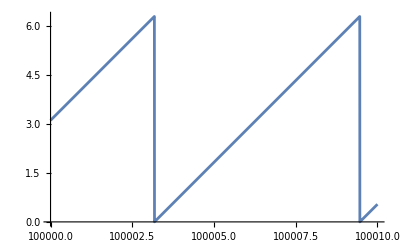

```mathematica
Plot[reduce[x],{x,100000,100010}]
```

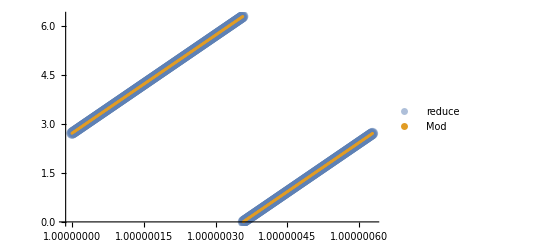

```mathematica
ListPlot[
{Table[{x,reduce[x]},{x,10000000,10000000+2Pi,0.01}],
Table[{x,N[Mod[x,2Pi],24]},{x,10000000,10000000+2Pi,0.01}]},
PlotLegends->{"reduce","Mod"},
PlotStyle->{{PointSize[0.02],Opacity[0.5]},{PointSize[0.005]}}
]
```

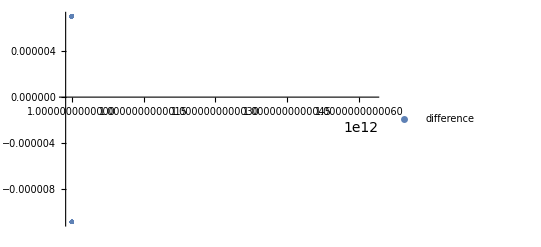

```mathematica
ListPlot[
Table[{x,reduce[x]-N[Mod[x,2Pi],18]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"difference"}]
```

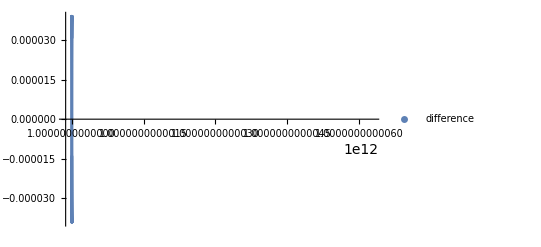

```mathematica
ListPlot[
Table[{x,sin3[x]-gslSin[x]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"difference"}]
```

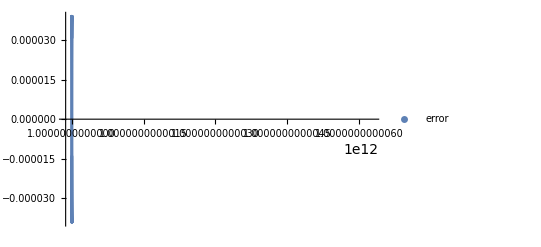

```mathematica
ListPlot[
Table[{x,sin3[x]-N[Sin[x]]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"error"}]
```

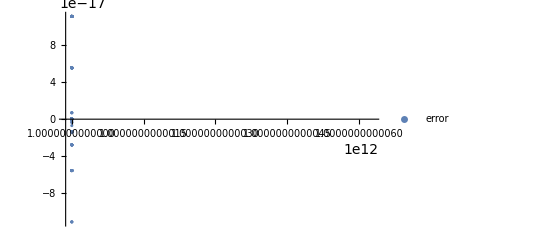

```mathematica
ListPlot[
Table[{x,gslSin[x]-N[Sin[x]]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"error"}]
```

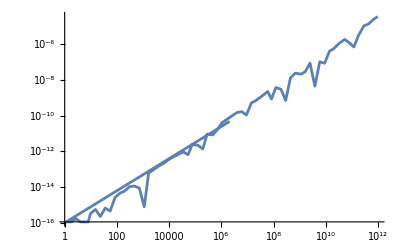

```mathematica
LogLogPlot[(Sin[#]-sin3[#]&)[x],{x,0, 10^12},PlotRange->All]
```

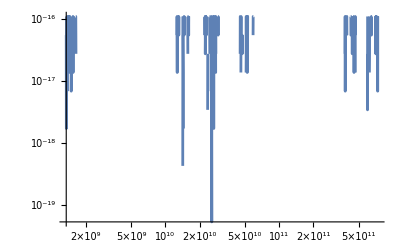

```mathematica
LogLogPlot[(Sin[#]-gslSin[#]&)[x],{x,0, 10^12},PlotRange->All]
```